```mathematica
Quit[]
```

#### Kernels Control

```mathematica
Once[LaunchKernels[4]]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
CloseKernels[Kernels[]]
```

```mathematica
Kernels[]
```

### Main

#### Declaration

```mathematica
ParallelEvaluate[Off[General::stop,NIntegrate::slwcon]];
```

```mathematica
(*ParallelEvaluate[On[General::stop]];*)
```

```mathematica
If[$OperatingSystem=="Windows",{dir="D:/Documents/2-d-data";},{dir="~/Documents/2-d-data";}];
```

```mathematica
ParallelEvaluate@SetOptions[NIntegrate,MaxRecursion->100,AccuracyGoal->10];
```

```mathematica
(*Old declaration, now packed into Package:OneFlavour`*)
```

The amplitude

```mathematica
(*If targeting the position, then use [ω1,ω2]*)
```

```mathematica
𝒞[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω2/(1+ω2-ω1),ω2->ω1/(1+ω2-ω1),ϕ1->ϕ3,ϕ3->ϕ1,ϕ2->ϕ4,ϕ4->ϕ2,M1->M3,M3->M1,M2->M4,M4->M2}]
𝒫[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->(1+ω2-ω1)/ω2,ω2->1/ω2,ϕ1->ϕ2,ϕ2->ϕ1,ϕ3->ϕ4,ϕ4->ϕ3,M1->M2,M2->M1,M3->M4,M4->M3}]
ℛ[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->ω1/ω2,ω2->1/ω2,ϕ3->ϕ4,ϕ4->ϕ3,M3->M4,M4->M3}]
𝒮[expr_[ω__][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]]:=ReplaceAll[expr[ω][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],{ω1->1/ω1,ω2->(1+ω2-ω1)/ω1,ϕ1->ϕ4,ϕ4->ϕ1,ϕ2->ϕ3,ϕ3->ϕ2,M1->M4,M4->M1,M2->M3,M3->M2}]
```

```mathematica
EXPR[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]+ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]+Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]];
```

```mathematica
ℳ0[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=4 g^2 ω1 NIntegrate[1/(y ω1-ω2-x)^2 ϕ1[(ω2-ω1+x)/(ω2-ω1+1)]ϕ2[y]ϕ3[x]ϕ4[(y ω1)/ω2],{x,0,1},{y,0,1}]
```

```mathematica
(*ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]=((#+𝒮[#])&[(*If[1>ω1,-4 g^2 NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,1},{y,0,1}],0]*)
ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒞[#])&[(*If[ω2>ω1,-4 g^2 NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}],0]*)
ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]])+((#+𝒮[#]+𝒫[#]+𝒞[#])&[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]);*)
ℐ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]},{y,0,(ω1-ω2+x ω2)/ω1-λ}]+NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]},{y,(ω1-ω2+x ω2)/ω1+λ,1}]-2/λ NIntegrate[ω2/ω1 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,If[#>0,#,0]&[(-ω1+λ ω1+ω2)/ω2 ],If[#<1,#,1]&[(-λ ω1+ω2)/ω2 ]}]+If[(-ω1+λ ω1+ω2)/ω2>0,NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,0,(-ω1+λ ω1+ω2)/ω2},{y,0,1}],0]+If[(-λ ω1+ω2)/ω2<1,NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,(-λ ω1+ω2)/ω2,1},{y,0,1}],0]);
ℐ2[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,M1_,M2_,M3_,M4_]:=-4 g^2(NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,If[#>0,#,0]&[ω1 λ],If[#<1,#,1]&[ω1 (1-λ)]}]+If[ω1 λ>0,NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,ω1 λ},{y,0,1}],0]+If[ω1 (1-λ)<1,NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,ω1 (1-λ),1},{y,0,1}],0]);
ℐ3[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][m_,Ma_,Mb_,Mc_,Md_]:=-(4 π)/Nc NIntegrate[(Mc^2+Md^2/ω2+(m^2-β^2)/(x-ω1)+(m^2-β^2)/(x-1)-(m^2-β^2)/(x-ω1+ω2)-(m^2-β^2)/x)ϕ1[(x-ω1+ω2)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[(x-ω1+ω2)/ω2],{x,0,1}];
```

```mathematica
EXPR1[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md];
```

```mathematica
ℳone[ω1_,ω2_][m_,Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=EXPR1[ω1,ω2][m,Ma,Mb,Mc,Md][ϕ1,ϕ2,ϕ3,ϕ4]
```

Solve ‘t Hooft equation

```mathematica
Clear[m1,m2,β,Nx]; (*β=1 unit*)
Nx=500;(*the size of the working matrix*)
β=1; (*the mass unit,definition β^2=g^2/(2Pi)Nc*)
(*m1=3.2*β;(*m1 and m2 are the bare masses of the quark and the anti-quark.*)
m2=3.2*β;*)
```

```mathematica
g=1;Nc=(β^2 π)/g^2;ℂ=0;(*ℂ denotes the interchange of final states.*)λ=10^-5;
```

```mathematica
vMatx[n_,m_]:=(vMatx[n-1,m-1] m/(m-1)+(8m)/(n+m-1)((1+(-1)^(n+m))/2))
vMatx[1,m_]:=4(1+(-1)^(m+1));
vMatx[n_,1]:=4/n(1+(-1)^(n+1));
```

```mathematica
Determineϕx[m1_,m2_,β_,Nx_]:=
Module[{HMatx,VMatx,vals,vecs,g,ϕx,ϕ},
SetSharedVariable[vecs,m1,m2,β,g];
SetSharedFunction[g];
HMatx=ParallelTable[4Min[n,m]((-1)^(n+m)(m1^2-β^2)+(m2^2-β^2)),{n,1,Nx},{m,1,Nx}];
VMatx=ParallelTable[vMatx[n,m],{n,1,Nx},{m,1,Nx}];
{vals,vecs}=Eigensystem[N[HMatx+VMatx]];
Do[g[j]=Dot[ParallelTable[Sin[i ArcCos[2x-1]],{i,1,Nx}],vecs[[j]]],{j,1,Nx}];
ϕx=ParallelTable[Quiet[g[Nx-n]/√NIntegrate[g[Nx-n]^2,{x,0,1}]],{n,0,20}];
Clear[g];
{√Reverse[vals] β,ϕx}
]
```

```mathematica
accDetermineϕ[m1_,m2_,β_,Nb_]:=
Module[{psi,ϵ=10^-6,Kernel1,Kernel2,hMT,sMT,sMatrix,hMTUp,hMT1,hMatrix,eg,vals,vecs,func,μ,nfunc},
Kernel1[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,0,x-ϵ}];
Kernel2[n_][x_?NumberQ]:=NIntegrate[psi[n,y]/(x-y)^2,{y,x+ϵ,1}];
psi[n_,x_]:=psi[n,x]=Which[n==0,x^(2-β)*(1-x)^β,n==1,(1-x)^(2-β)*x^β,n≥2,Sin[(n-1)*π*x]];
hMT[m_,n_]:=hMT[m,n]=NIntegrate[psi[m,x]((m1^2-1)/(x*(1-x))*psi[n,x]-Kernel1[n][x]-Kernel2[n][x]+(2psi[n,x])/ϵ),{x,ϵ,1-ϵ},WorkingPrecision->20];
sMT[m_,n_]:=sMT[m,n]=NIntegrate[psi[m,x]psi[n,x],{x,0,1}];
sMatrix=ParallelTable[Quiet[sMT[m,n]],{m,0,Nb},{n,0,Nb}]//Chop;hMTUp=PadLeft[#,Nb+1]&/@ParallelTable[Quiet[hMT[m,n]],{m,0,Nb},{n,m,Nb}];
(*Print[hMTUp];*)
hMatrix=Transpose[hMTUp]+hMTUp-DiagonalMatrix[Diagonal[hMTUp]];
(*Print[MatrixForm[hMatrix]];*)
eg[μ_]:=Det[hMatrix-μ^2*sMatrix];
μ=Sort@DeleteDuplicatesBy[Table[μ/.FindRoot[eg[μ]==0,{μ,a,a+0.2}],{a,0,Nb^2,0.2}],SetPrecision[#,2]&];
Print[μ];
vecs=(Flatten@NullSpace[hMatrix-#^2 sMatrix,Tolerance->0.001])&/@μ;
Print[vecs];Print[Dimensions@vecs];
func=ParallelTable[Table[psi[i,x],{i,0,Nb}].vecs[[j]],{j,1,Length[vecs]}];
nfunc=ParallelTable[Quiet[func[[n]]/√NIntegrate[func[[n]]^2,{x,0,1}]],{n,1,20}];
Clear[func,vecs];
{μ,nfunc}
]
```

```mathematica
ϕn[n_][ϕ_][x_]:=ϕ[x][[n+1]];
```

```mathematica
Mn[n_][vals_]:=vals[[n+1]];
```

Used z=(r_(2-))/(r_(1-)+r_(2-)), ω=(r_(4-))/(r_(1-)+r_(2-)), ω_1=(r_(2-))/(r_(3-)), ω_2=(r_(4-))/(r_(3-)) here.

```mathematica
(*ω2p[ω1_][M1_,M2_,M3_,M4_]:=1/(2 (M3^2 ω1-M2^2))(-√((M1^2 (-ω1)+M2^2 ω1-M2^2-M3^2 ω1^2+M3^2 ω1+M4^2 ω1)^2-4 (M4^2 ω1-M4^2 ω1^2) (M3^2 ω1-M2^2))+M1^2 ω1-M2^2 ω1+M2^2+M3^2 ω1^2-M3^2 ω1-M4^2 ω1)(*transform ω1 to ω2, your definition, solution 1*)*)
```

```mathematica
(*Sω1[ω1_][M1_,M2_,M3_,M4_]:=(M1^2/(1-ω1+ω2p[ω1][M1,M2,M3,M4])+M2^2/ω1)(1+ω2p[ω1][M1,M2,M3,M4]);*)
```

```mathematica
ω1S[s_][M1_,M2_,M3_,M4_]:=(-M1^2+M2^2+s-√s √((M1^4+(M2^2-s)^2-2 M1^2 (M2^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
ω2S[s_][M1_,M2_,M3_,M4_]:=(-M3^2+M4^2+s-√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s))/(M3^2-M4^2+s+√s √((M3^4+(M4^2-s)^2-2 M3^2 (M4^2+s))/s));
```

```mathematica
Msum[mQ_][n1_?IntegerQ,n2_?IntegerQ,n3_?IntegerQ,n4_?IntegerQ]:=
Module[{ϕxB,ΦB,ValsB,ϕxπ,Φπ,Valsπ,M1,M2,M3,ϕ1,ϕ2,ϕ3,Ares,filename,ωnow,m1,m2,M4,ϕ4,ω1,ω2,Sen,filenameacc,Determine,Mseq,ΦBi},
(*SetSharedVariable[m2,m1];*)
m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or to use the original solution suggested by 't Hooft, ",{"BSW method"->True,"Brute force integration"->False}],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],Boole[0≤x≤1]ϕxB};
}
];
(*Set@@{ΦB[x_?NumberQ],If[0<x<1,ΦBi[x],Table[0,{n,Length@ϕxB}]]};*)
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[n3];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[n4];
Mseq=Sequence[M1,M2,M3,M4];
Print["M1=",M1,"  M2=",M2,"  M3=",M3,"  M4=",M4];
{{M1,M2,M3,M4},ParallelTable[Sen=Ssqur^2;ω1=ω1S[Sen][M1,M2,M3,M4];ω2=ω2S[Sen][M1,M2,M3,M4];
{Ssqur,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][mQ,M1,M2,M3,M4]},{Ssqur,M1+M2,M1+M2+2,0.01}]}
]
```

#### Calc

```mathematica
Clear["Global`g$*"]
```

```mathematica
Information["Global`g$*"]
```

```mathematica
Clear["OneFlavour`"]
```

```mathematica
AppendTo[$Path,NotebookDirectory[]];
Get["OneFlavour`"]
```

```mathematica
displayfunction1::usage="displayfunction1[Msumdat,{min,max}], amplitude plot, min/max is the spare space in both ends. ";
displayfunction1::usage="displayfunction2[Msumdat,{min,max}], amplitude square plot, min/max is the spare space in both ends. ";
```

```mathematica
displayfunction1[Msumdat_,{min_,max_},opt:OptionsPattern[{Joined->True,LegendMargins->3}]]:=ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],Last[Msumdat[[2]]][[2]]},{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{First[Msumdat[[2]]][[1]]+min,Last[Msumdat[[2]]][[1]]+max},All},FilterRules[{opt},Options[ListPlot]],PlotLabel->"Amp: Threshold: "<>ToString[If[Msumdat[[1,1,1]]+Msumdat[[1,1,2]]>=Msumdat[[1,1,3]]+Msumdat[[1,1,4]],Msumdat[[1,2,1]]+Msumdat[[1,2,2]],Msumdat[[1,2,3]]+Msumdat[[1,2,4]]]]<>" MeV",ImageSize->Medium,PlotLegends->Placed[LineLegend[{ToString[Msumdat[[1,1,1]]]<>"+"<>ToString[Msumdat[[1,1,2]]]<>"→"<>ToString[Msumdat[[1,1,3]]]<>"+"<>ToString[Msumdat[[1,1,4]]]},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->OptionValue[LegendMargins],LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","ℳ"},PlotStyle->{{Automatic},{Dotted}}];
displayfunction2[Msumdat_,{min_,max_},opt:OptionsPattern[{Joined->True,LegendMargins->3}]]:=ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],(Last[Msumdat[[2]]][[2]])^2},{Msumdat[[1,2,1]]+Msumdat[[1,2,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{First[Msumdat[[2]]][[1]]+min,Last[Msumdat[[2]]][[1]]+max},All},FilterRules[{opt},Options[ListPlot]],PlotLabel->"Amp square: Threshold: "<>ToString[If[Msumdat[[1,1,1]]+Msumdat[[1,1,2]]>=Msumdat[[1,1,3]]+Msumdat[[1,1,4]],Msumdat[[1,2,1]]+Msumdat[[1,2,2]],Msumdat[[1,2,3]]+Msumdat[[1,2,4]]]]<>" MeV",ImageSize->Medium,PlotLegends->Placed[LineLegend[{ToString[Msumdat[[1,1,1]]]<>"+"<>ToString[Msumdat[[1,1,2]]]<>"→"<>ToString[Msumdat[[1,1,3]]]<>"+"<>ToString[Msumdat[[1,1,4]]]},LegendLayout->{"Column",1}(*,LegendMarkerSize->20*),LegendMargins->OptionValue[LegendMargins],LegendFunction->"Frame"],{Right,Top}],Frame->True,FrameLabel->{"MeV","|ℳ|^2"},PlotStyle->{{Automatic},{Dotted}}]
```

```mathematica
Clear[ϕx,m2,ϕ,vals,M1,M2,M3,ϕ1,ϕ2,ϕ3];
```

#### 2→2

The total amplitude (and the square):

```mathematica
Msumdat=Msum[60,{0,0,0,0},SRange->{10^-3,1,0.01},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.335  M4=120.335

{{120.335,120.335,120.335,120.335},{{240.672,2449.24},{240.682,2162.97},{240.692,1891.59},{240.702,1640.5},{240.712,1304.3},{240.722,1094.12},{240.732,973.309},{240.742,777.49},{240.752,585.98},{240.762,412.85},{240.772,250.995},{240.782,99.7097},{240.792,-42.0596},{240.802,-174.385},{240.812,-297.684},{240.822,-413.078},{240.832,-520.437},{240.842,-620.944},{240.852,-714.379},{240.862,-801.311},{240.872,-882.198},{240.882,-941.101},{240.892,-1012.38},{240.902,-1075.28},{240.912,-1133.99},{240.922,-1188.14},{240.932,-1269.16},{240.942,-1310.75},{240.952,-1351.5},{240.962,-1386.61},{240.972,-1450.8},{240.982,-1466.84},{240.992,-1488.63},{241.002,-1514.36},{241.012,-1538.02},{241.022,-1559.29},{241.032,-1566.14},{241.042,-1583.97},{241.052,-1598.84},{241.062,-1612.2},{241.072,-1623.79},{241.082,-1633.64},{241.092,-1641.92},{241.102,-1654.},{241.112,-1655.19},{241.122,-1659.26},{241.132,-1661.86},{241.142,-1663.48},{241.152,-1664.02},{241.162,-1663.57},{241.172,-1662.16},{241.182,-1659.79},{241.192,-1656.8},{241.202,-1657.75},{241.212,-1652.98},{241.222,-1650.71},{241.232,-1644.78},{241.242,-1638.61},{241.252,-1631.95},{241.262,-1624.69},{241.272,-1616.97},{241.282,-1608.87},{241.292,-1600.42},{241.302,-1591.63},{241.312,-1582.49},{241.322,-1573.09},{241.332,-1563.44},{241.342,-1553.6},{241.352,-1543.53},{241.362,-1533.27},{241.372,-1522.85},{241.382,-1512.28},{241.392,-1501.59},{241.402,-1490.77},{241.412,-1480.41},{241.422,-1468.56},{241.432,-1457.78},{241.442,-1446.65},{241.452,-1435.49},{241.462,-1424.31},{241.472,-1413.1},{241.482,-1401.62},{241.492,-1390.4},{241.502,-1379.16},{241.512,-1367.98},{241.522,-1356.8},{241.532,-1345.64},{241.542,-1334.53},{241.552,-1323.44},{241.562,-1312.44},{241.572,-1301.45},{241.582,-1290.51},{241.592,-1279.64},{241.602,-1268.81},{241.612,-1258.07},{241.622,-1247.4},{241.632,-1236.81},{241.642,-1226.29},{241.652,-1215.92},{241.662,-1205.5}}}

```mathematica
AbsoluteTiming[Msumdat=Msum[60,{0,0,0,0},SRange->{10^-3,2,0.05},Lambda->10^-5]]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.335  M4=120.335

{3155.68,{{120.335,120.335,120.335,120.335},{{240.672,2449.24},{240.722,1094.12},{240.772,250.995},{240.822,-413.078},{240.872,-882.198},{240.922,-1188.14},{240.972,-1450.8},{241.022,-1559.29},{241.072,-1623.79},{241.122,-1659.26},{241.172,-1662.16},{241.222,-1650.71},{241.272,-1616.97},{241.322,-1573.09},{241.372,-1522.85},{241.422,-1468.56},{241.472,-1413.1},{241.522,-1356.8},{241.572,-1301.45},{241.622,-1247.4},{241.672,-1195.22},{241.722,-1145.11},{241.772,-1097.28},{241.822,-1051.84},{241.872,-1008.78},{241.922,-968.067},{241.972,-929.596},{242.022,-893.317},{242.072,-859.124},{242.122,-826.896},{242.172,-796.53},{242.222,-767.909},{242.272,-740.935},{242.322,-715.496},{242.372,-691.498},{242.422,-668.836},{242.472,-647.421},{242.522,-627.174},{242.572,-608.013},{242.622,-589.87}}}}

```mathematica
Msumdat={%12[[1]],%12[[2]]~Join~%10[[2,2]]};
```

```mathematica
Msumdat[[2]]=Sort@Msumdat[[2]];
```

```mathematica
Msumdat[[2]]=DeleteDuplicates@Msumdat[[2]];
```

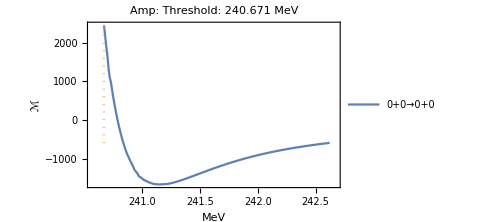
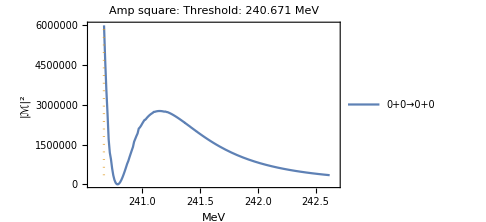

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,2}],displayfunction2[Msumdat,{-0.1,2}]}]
```

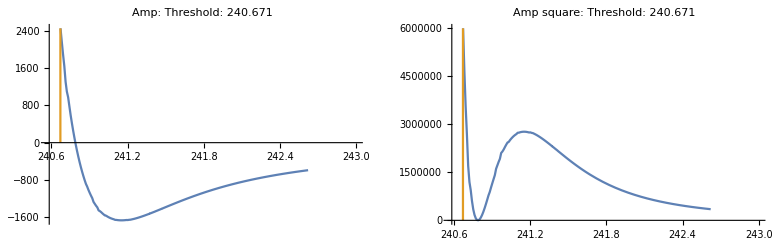

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,243},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,243},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{1,1,1,1},SRange->{10^-3,0.5,0.01},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.79  M2=120.79  M3=120.79  M4=120.79

{{120.79,120.79,120.79,120.79},{{241.581,-3644.33},{241.591,-4080.22},{241.601,-4405.19},{241.611,-4640.22},{241.621,-4796.55},{241.631,-4885.79},{241.641,-4918.78},{241.651,-4904.98},{241.661,-4852.53},{241.671,-4768.98},{241.681,-4660.8},{241.691,-4532.39},{241.701,-4389.52},{241.711,-4236.27},{241.721,-4075.68},{241.731,-3910.75},{241.741,-3744.11},{241.751,-3579.11},{241.761,-3415.28},{241.771,-3254.64},{241.781,-3099.72},{241.791,-2949.05},{241.801,-2805.56},{241.811,-2668.94},{241.821,-2540.75},{241.831,-2419.88},{241.841,-2305.19},{241.851,-2123.59},{241.861,-2021.75},{241.871,-1929.22},{241.881,-1929.26},{241.891,-1853.42},{241.901,-1785.21},{241.911,-1729.89},{241.921,2.31676×10^6},{241.931,-1620.99},{241.941,-1578.3},{241.951,-1540.01},{241.961,-1509.7},{241.971,-1482.02},{241.981,-1460.57},{241.991,-1441.75},{242.001,-1427.76},{242.011,-1417.06},{242.021,-1409.9},{242.031,-1405.49},{242.041,-1393.72},{242.051,-1394.6},{242.061,-1403.69},{242.071,-1408.74}}}

```mathematica
Msumdat=Msum[60,{1,1,1,1},SRange->{0.51,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.79  M2=120.79  M3=120.79  M4=120.79

{{120.79,120.79,120.79,120.79},{{242.09,-1429.09},{242.12,-1478.99},{242.15,-1503.38},{242.18,-1576.51},{242.21,-1611.9},{242.24,-1656.32},{242.27,-1701.19},{242.3,-1738.11},{242.33,-1737.88},{242.36,-1794.22},{242.39,-1812.97},{242.42,-1825.5},{242.45,-1832.43},{242.48,-1834.76},{242.51,-1831.2},{242.54,-1821.96},{242.57,-1808.44},{242.6,-1791.04},{242.63,-1770.25},{242.66,-1746.01},{242.69,-1719.35},{242.72,-1690.99},{242.75,-1658.39},{242.78,-1565.54},{242.81,-1596.93},{242.84,-1563.64},{242.87,-1529.7},{242.9,-1495.54},{242.93,-1461.22},{242.96,-1426.9},{242.99,-1392.83},{243.02,-1359.17},{243.05,-1325.87},{243.08,-789.649},{243.11,-1261.24},{243.14,-1230.02},{243.17,-1180.53},{243.2,-1169.13},{243.23,-1140.04},{243.26,-1111.56},{243.29,-1083.64},{243.32,-1056.81},{243.35,-1030.57},{243.38,-1005.35},{243.41,-980.937},{243.44,-957.04},{243.47,-934.454},{243.5,-912.366},{243.53,-891.029},{243.56,-870.396}}}

```mathematica
Msumdat={%7[[1]],%7[[2]]~Join~%8[[2]]};
```

```mathematica
Msumdat=Delete[Msumdat,{2,-17}];
```

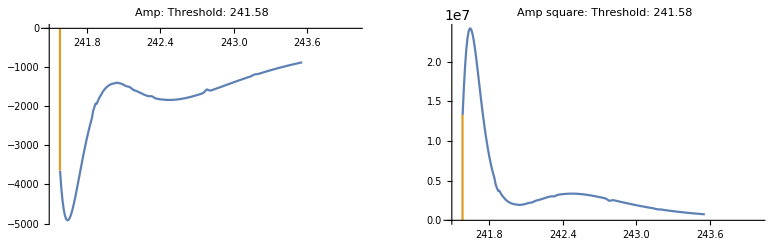

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,2,2,2},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=121.104  M4=121.104

{{121.104,121.104,121.104,121.104},{{242.208,-6484.36},{242.238,-7357.1},{242.268,-6895.85},{242.298,-6069.43},{242.328,-5318.48},{242.358,-4792.04},{242.388,-4499.01},{242.418,-4386.41},{242.448,-4377.6},{242.478,-4424.39},{242.508,-4483.5},{242.538,-4494.},{242.568,-4375.85},{242.598,-4348.73},{242.628,-4131.76},{242.658,-3983.77},{242.688,-3743.17},{242.718,-3474.83},{242.748,-3194.66},{242.778,-2912.18},{242.808,-2635.12},{242.838,-2377.78},{242.868,-2138.02},{242.898,-1922.07},{242.928,-1731.72},{242.958,-1568.03},{242.988,-1456.87},{243.018,-1317.68},{243.048,-1228.69},{243.078,-1169.7},{243.108,-1112.03},{243.138,-1078.66},{243.168,-1060.29},{243.198,-1053.15},{243.228,-1055.85},{243.258,-1075.79},{243.288,-1090.07},{243.318,-1105.3},{243.348,-1131.82},{243.378,-1142.9},{243.408,-1165.73},{243.438,-1188.04},{243.468,-1209.19},{243.498,-1228.38},{243.528,-1245.9},{243.558,-1260.4},{243.588,-1272.86},{243.618,-1282.28},{243.648,-1289.1},{243.678,-1293.28},{243.708,-1294.79},{243.738,-1285.12},{243.768,-1290.49},{243.798,-1285.01},{243.828,-1277.56},{243.858,-1268.22},{243.888,-1256.65},{243.918,-1244.43},{243.948,-1230.65},{243.978,-1215.24},{244.008,-1199.09},{244.038,-1182.02},{244.068,-1164.24},{244.098,-1145.89},{244.128,-1127.03},{244.158,-1107.86},{244.188,-1088.3}}}

```mathematica
Msumdat=Msum[60,{2,2,2,2},SRange->{10^-3,0.5,0.01},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=121.104  M4=121.104

{{121.104,121.104,121.104,121.104},{{242.208,-6484.36},{242.218,-7014.64},{242.228,-7281.77},{242.238,-7357.1},{242.248,-7242.48},{242.258,-7076.02},{242.268,-6895.85},{242.278,-6631.67},{242.288,-6350.83},{242.298,-6069.43},{242.308,-5800.67},{242.318,-5547.02},{242.328,-5318.48},{242.338,-5113.45},{242.348,-4939.82},{242.358,-4792.04},{242.368,-4670.32},{242.378,-4573.73},{242.388,-4499.01},{242.398,-4446.39},{242.408,-4406.23},{242.418,-4386.41},{242.428,-4377.},{242.438,-4377.49},{242.448,-4377.6},{242.458,-4391.22},{242.468,-4407.22},{242.478,-4424.39},{242.488,-4455.13},{242.498,-4470.59},{242.508,-4483.5},{242.518,-4491.92},{242.528,-4495.58},{242.538,-4494.},{242.548,-4485.36},{242.558,-4471.84},{242.568,-4375.85},{242.578,-4403.08},{242.588,-4389.55},{242.598,-4348.73},{242.608,-4301.88},{242.618,-4248.87},{242.628,-4131.76},{242.638,-4126.18},{242.648,-4056.67},{242.658,-3983.77},{242.668,-3908.15},{242.678,-3825.91},{242.688,-3743.17},{242.698,-3655.18}}}

```mathematica
Msumdat={%12[[1]],%12[[2]]~Join~Drop[%9[[2]],17]};
```

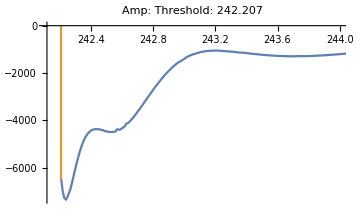
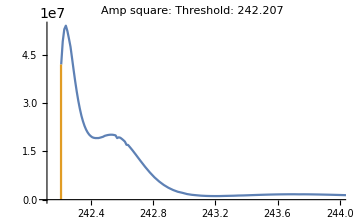

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{1,1,0,0},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.79  M2=120.79  M3=120.335  M4=120.335

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{{1,1,0,0},{120.79,120.79,120.335,120.335}},{{241.581,340.535},{241.611,502.032},{241.641,632.905},{241.671,741.194},{241.701,826.36},{241.731,896.093},{241.761,946.238},{241.791,983.308},{241.821,1008.8},{241.851,1024.89},{241.881,1032.28},{241.911,1032.18},{241.941,1026.8},{241.971,1016.71},{242.001,1002.74},{242.031,985.633},{242.061,966.044},{242.091,944.487},{242.121,921.54},{242.151,897.606},{242.181,872.896},{242.211,847.789},{242.241,822.46},{242.271,797.073},{242.301,771.993},{242.331,747.119},{242.361,722.679},{242.391,698.728},{242.421,675.273},{242.451,652.472},{242.481,630.292},{242.511,608.781},{242.541,587.945},{242.571,567.804},{242.601,548.357},{242.631,529.596},{242.661,511.52},{242.691,494.114},{242.721,477.374},{242.751,461.274},{242.781,445.802},{242.811,430.94},{242.841,416.651},{242.871,402.948},{242.901,389.794},{242.931,377.174},{242.961,365.06},{242.991,353.436},{243.021,342.278},{243.051,331.574},{243.081,321.302},{243.111,311.444},{243.141,301.982},{243.171,292.899},{243.201,284.178},{243.231,275.801},{243.261,267.76},{243.291,260.033},{243.321,252.607},{243.351,245.469},{243.381,238.609},{243.411,232.011},{243.441,225.667},{243.471,219.56},{243.501,213.686},{243.531,208.029},{243.561,202.583}}}

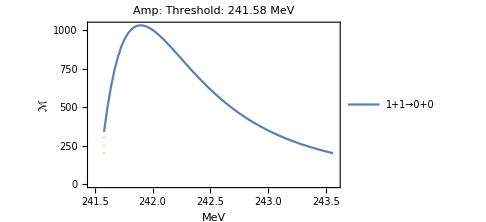
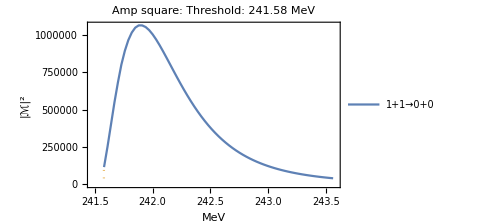

```mathematica
Row[{displayfunction1[Msumdat],displayfunction2[Msumdat]}]
```

```mathematica
Msumdat=Msum[60,{1,1,1,0},SRange->{10^-3,2,0.03},Lambda->10^-6]
```

Wavefunction build complete.

M1=120.79  M2=120.79  M3=120.79  M4=120.335

{{120.79,120.79,120.79,120.335},{{241.581,0.000647906},{241.611,-0.000519235},{241.641,-0.00193154},{241.671,-0.002065},{241.701,-0.00253345},{241.731,-0.00262575},{241.761,-0.00265012},{241.791,-0.00265667},{241.821,-0.00282828},{241.851,-0.00261471},{241.881,-0.00268764},{241.911,-0.00233973},{241.941,-0.00206643},{241.971,-0.00190701},{242.001,-0.00190614},{242.031,-0.00166953},{242.061,-0.00143253},{242.091,-0.00151777},{242.121,-0.00137075},{242.151,-0.00124103},{242.181,-0.00100615},{242.211,-0.00102972},{242.241,-0.000944099},{242.271,-0.000838774},{242.301,-0.000698729},{242.331,-0.000663129},{242.361,-0.000622141},{242.391,-0.000543628},{242.421,-0.000542697},{242.451,-0.000401541},{242.481,-0.00039414},{242.511,-0.000339085},{242.541,-0.000346672},{242.571,-0.000278766},{242.601,-0.0002703},{242.631,-0.000253322},{242.661,-0.000225841},{242.691,-0.000202142},{242.721,-0.0000387166},{242.751,-0.000164686},{242.781,-0.000155121},{242.811,-0.000140142},{242.841,-0.000123538},{242.871,-0.000107295},{242.901,-0.000108336},{242.931,-0.000084471},{242.961,-0.0000771707},{242.991,-0.0000833592},{243.021,-0.000077172},{243.051,-0.0000702707},{243.081,-0.0000664551},{243.111,-0.0000658564},{243.141,-0.0000592559},{243.171,-0.00005583},{243.201,-0.0000483258},{243.231,-0.0000394598},{243.261,-0.0000401066},{243.291,-0.0000374503},{243.321,-0.0000346111},{243.351,-0.000031131},{243.381,-0.0000292838},{243.411,-0.0000299405},{243.441,-0.0000262627},{243.471,-0.0000224408},{243.501,-0.0000220807},{243.531,-0.0000200369},{243.561,-0.0000186783}}}

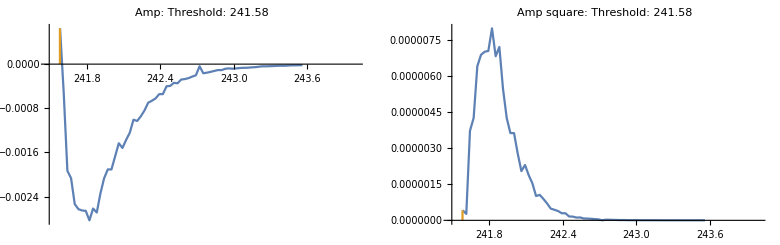

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{1,0,0,0},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.79  M2=120.335  M3=120.335  M4=120.335

{{120.79,120.335,120.335,120.335},{{241.126,-0.0000167404},{241.156,-0.0000265934},{241.186,-0.0000230159},{241.216,-0.0000213965},{241.246,-0.0000189066},{241.276,-0.000018977},{241.306,-0.0000190098},{241.336,-0.0000177895},{241.366,-0.0000149731},{241.396,-0.0000125435},{241.426,-0.0000133193},{241.456,-0.0000121494},{241.486,-0.0000100792},{241.516,-9.47314×10^-6},{241.546,-8.46543×10^-6},{241.576,-9.16214×10^-6},{241.606,-8.11025×10^-6},{241.636,-6.47443×10^-6},{241.666,-5.17853×10^-6},{241.696,-4.75513×10^-6},{241.726,-4.51961×10^-6},{241.756,-3.97575×10^-6},{241.786,-3.49632×10^-6},{241.816,-3.06913×10^-6},{241.846,-2.98571×10^-6},{241.876,-2.43481×10^-6},{241.906,-2.36286×10^-6},{241.936,-2.02913×10^-6},{241.966,-1.55058×10^-6},{241.996,-1.47812×10^-6},{242.026,-1.23458×10^-6},{242.056,-1.17227×10^-6},{242.086,-2.44502×10^-6},{242.116,-2.56419×10^-6},{242.146,-2.75804×10^-6},{242.176,-2.92773×10^-6},{242.206,-2.6262×10^-6},{242.236,-2.26623×10^-6},{242.266,-2.02078×10^-6},{242.296,-2.30312×10^-6},{242.326,-2.25295×10^-6},{242.356,-2.3275×10^-6},{242.386,-2.39887×10^-6},{242.416,-2.4835×10^-6},{242.446,-2.48875×10^-6},{242.476,-2.32312×10^-6},{242.506,-1.99748×10^-6},{242.536,-1.66658×10^-6},{242.566,-1.59682×10^-6},{242.596,-1.8399×10^-6},{242.626,-7.8047×10^-6},{242.656,-2.59484×10^-6},{242.686,-4.14091×10^-6},{242.716,-2.27558×10^-6},{242.746,-1.62386×10^-6},{242.776,-1.26411×10^-6},{242.806,-7.56996×10^-7},{242.836,-8.61944×10^-7},{242.866,-1.33378×10^-6},{242.896,-1.81733×10^-6},{242.926,-2.06854×10^-6},{242.956,-1.98082×10^-6},{242.986,-1.60749×10^-6},{243.016,-1.12036×10^-6},{243.046,-6.63279×10^-7},{243.076,-4.47832×10^-7},{243.106,-4.79448×10^-7}}}

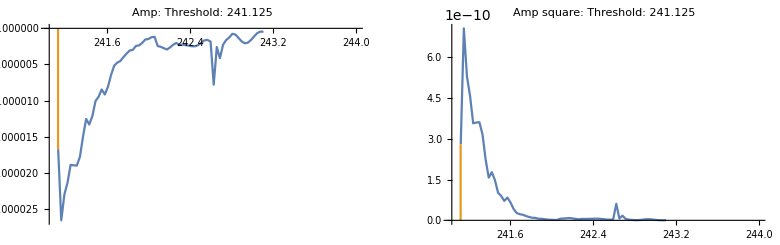

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{0,1,0,0},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=120.335  M2=120.79  M3=120.335  M4=120.335

{{120.335,120.79,120.335,120.335},{{241.126,0.0000254766},{241.156,0.0000319626},{241.186,0.0000288186},{241.216,0.0000268688},{241.246,0.0000269293},{241.276,0.0000260391},{241.306,0.000023396},{241.336,0.0000195896},{241.366,0.0000170277},{241.396,0.0000154859},{241.426,0.0000134537},{241.456,0.0000138101},{241.486,0.0000105409},{241.516,9.72848×10^-6},{241.546,0.0000100308},{241.576,8.66703×10^-6},{241.606,7.83887×10^-6},{241.636,7.65523×10^-6},{241.666,5.80356×10^-6},{241.696,5.25734×10^-6},{241.726,4.65405×10^-6},{241.756,4.74851×10^-6},{241.786,4.28254×10^-6},{241.816,3.15321×10^-6},{241.846,2.92075×10^-6},{241.876,2.72472×10^-6},{241.906,2.38825×10^-6},{241.936,2.15365×10^-6},{241.966,1.74633×10^-6},{241.996,1.71545×10^-6},{242.026,1.46679×10^-6},{242.056,1.3511×10^-6},{242.086,1.28293×10^-6},{242.116,1.18623×10^-6},{242.146,1.06183×10^-6},{242.176,1.06264×10^-6},{242.206,7.55554×10^-7},{242.236,8.41779×10^-7},{242.266,7.65754×10^-7},{242.296,7.11395×10^-7},{242.326,6.30788×10^-7},{242.356,5.84277×10^-7},{242.386,5.66342×10^-7},{242.416,5.32022×10^-7},{242.446,4.68069×10^-7},{242.476,4.92331×10^-7},{242.506,4.74303×10^-7},{242.536,4.82643×10^-7},{242.566,4.54757×10^-7},{242.596,-4.01774×10^-8},{242.626,-9.70809×10^-8},{242.656,-1.85937×10^-7},{242.686,-2.44711×10^-7},{242.716,-2.08332×10^-7},{242.746,-2.73053×10^-7},{242.776,-3.11847×10^-7},{242.806,-2.50578×10^-7},{242.836,-2.40608×10^-7},{242.866,-3.3928×10^-7},{242.896,-3.72588×10^-7},{242.926,-3.31675×10^-7},{242.956,-2.23839×10^-7},{242.986,-8.59736×10^-8},{243.016,-1.89735×10^-8},{243.046,3.18564×10^-8},{243.076,-1.4821×10^-8},{243.106,-6.78809×10^-8}}}

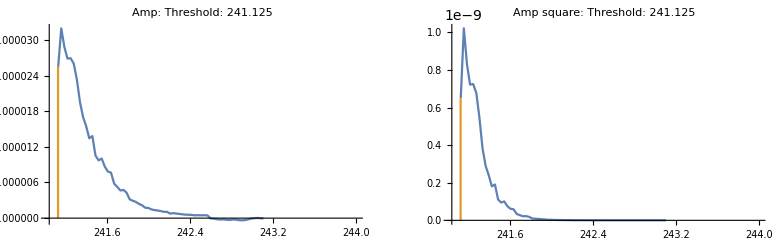

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,0,0,0},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=120.335  M3=120.335  M4=120.335

{{121.104,120.335,120.335,120.335},{{241.44,-1214.64},{241.47,-970.956},{241.5,-756.251},{241.53,-567.627},{241.56,-405.013},{241.59,-264.244},{241.62,-142.349},{241.65,-31.3777},{241.68,50.52},{241.71,126.471},{241.74,189.31},{241.77,241.924},{241.8,285.388},{241.83,320.816},{241.86,349.658},{241.89,372.342},{241.92,389.834},{241.95,402.706},{241.98,412.126},{242.01,418.073},{242.04,421.018},{242.07,421.821},{242.1,420.625},{242.13,417.702},{242.16,413.426},{242.19,407.994},{242.22,401.711},{242.25,394.635},{242.28,386.953},{242.31,378.824},{242.34,370.38},{242.37,361.669},{242.4,352.815},{242.43,343.849},{242.46,334.852},{242.49,325.89},{242.52,316.978},{242.55,308.18},{242.58,299.51},{242.61,291.002},{242.64,282.662},{242.67,274.497},{242.7,266.533},{242.73,258.771},{242.76,251.219},{242.79,243.88},{242.82,236.757},{242.85,229.853},{242.88,223.163},{242.91,216.677},{242.94,210.41},{242.97,204.341},{243.,198.476},{243.03,192.808},{243.06,187.334},{243.09,182.047},{243.12,176.94},{243.15,172.011},{243.18,167.249},{243.21,162.658},{243.24,158.224},{243.27,153.947},{243.3,149.817},{243.33,145.831},{243.36,141.983},{243.39,138.269},{243.42,134.684}}}

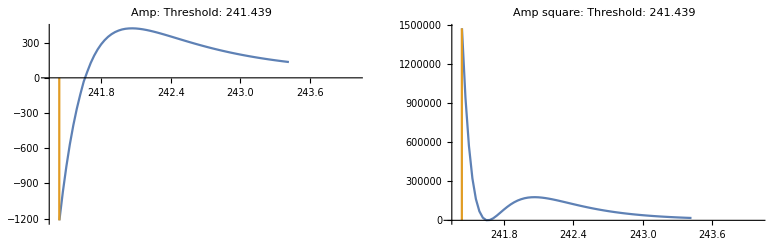

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,1,0,0},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=120.79  M3=120.335  M4=120.335

{{121.104,120.79,120.335,120.335},{{241.895,-0.000010267},{241.925,-0.0000157358},{241.955,-0.0000132857},{241.985,-0.0000150813},{242.015,-0.0000148394},{242.045,-0.0000130045},{242.075,-0.0000129813},{242.105,-9.82866×10^-6},{242.135,-9.89359×10^-6},{242.165,-0.0000104251},{242.195,-8.11263×10^-6},{242.225,-8.16742×10^-6},{242.255,-7.54156×10^-6},{242.285,-7.06255×10^-6},{242.315,-5.45036×10^-6},{242.345,-6.42781×10^-6},{242.375,-5.72002×10^-6},{242.405,-4.77411×10^-6},{242.435,-4.5702×10^-6},{242.465,-3.66211×10^-6},{242.495,-3.25162×10^-6},{242.525,-2.7788×10^-6},{242.555,-2.45529×10^-6},{242.585,-2.42766×10^-6},{242.615,-2.11716×10^-6},{242.645,-1.90141×10^-6},{242.675,-1.72879×10^-6},{242.705,-1.61166×10^-6},{242.735,-1.415×10^-6},{242.765,-1.04249×10^-6},{242.795,-1.10682×10^-6},{242.825,-1.04968×10^-6},{242.855,-9.43893×10^-7},{242.885,-8.91094×10^-7},{242.915,-1.43077×10^-6},{242.945,-1.06962×10^-6},{242.975,-7.64488×10^-7},{243.005,-3.75498×10^-7},{243.035,-1.29741×10^-7},{243.065,-2.46646×10^-8},{243.095,3.11029×10^-7},{243.125,5.70248×10^-7},{243.155,8.02287×10^-7},{243.185,9.79571×10^-7},{243.215,1.08585×10^-6},{243.245,1.15795×10^-6},{243.275,1.20577×10^-6},{243.305,1.28446×10^-6},{243.335,1.39823×10^-6},{243.365,1.49834×10^-6},{243.395,1.47943×10^-6},{243.425,1.40387×10^-6},{243.455,1.31422×10^-6},{243.485,1.25701×10^-6},{243.515,1.21221×10^-6},{243.545,1.20885×10^-6},{243.575,1.03907×10^-6},{243.605,9.51733×10^-7},{243.635,1.00168×10^-6},{243.665,8.50599×10^-7},{243.695,7.10709×10^-7},{243.725,6.21523×10^-7},{243.755,5.60713×10^-7},{243.785,1.13935×10^-6},{243.815,6.92379×10^-7},{243.845,1.34691×10^-7},{243.875,-2.89099×10^-7}}}

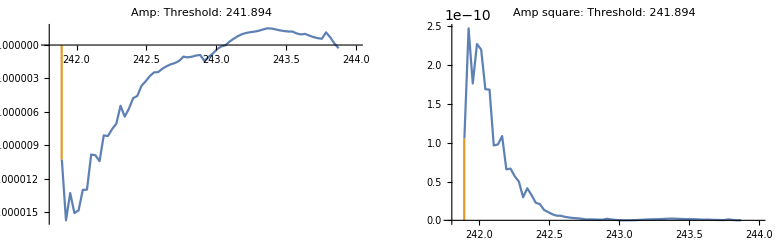

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{10,5,0,0},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=122.906  M2=121.886  M3=120.335  M4=120.335

{{122.906,121.886,120.335,120.335},{{244.793,-2.03355×10^-6},{244.823,-5.12688×10^-6},{244.853,-4.29703×10^-6},{244.883,-4.93714×10^-6},{244.913,-5.63768×10^-6},{244.943,-4.87854×10^-6},{244.973,-5.02237×10^-6},{245.003,-4.33642×10^-6},{245.033,-4.03338×10^-6},{245.063,-3.82267×10^-6},{245.093,-3.6851×10^-6},{245.123,-3.39319×10^-6},{245.153,-3.60661×10^-6},{245.183,-2.11013×10^-6},{245.213,-2.72134×10^-6},{245.243,-2.34793×10^-6},{245.273,-2.21939×10^-6},{245.303,-2.20681×10^-6},{245.333,-1.90191×10^-6},{245.363,-1.86386×10^-6},{245.393,-1.68295×10^-6},{245.423,-1.52065×10^-6},{245.453,-2.33337×10^-6},{245.483,-1.70188×10^-6},{245.513,-1.07585×10^-6},{245.543,-7.24591×10^-7},{245.573,-3.18×10^-7},{245.603,-1.41081×10^-7},{245.633,-4.14433×10^-8},{245.663,-9.42394×10^-8},{245.693,-1.61029×10^-7},{245.723,-3.26743×10^-7},{245.753,-5.33958×10^-7},{245.783,-5.2821×10^-7},{245.813,-4.61773×10^-7},{245.843,-4.68368×10^-7},{245.873,-5.10377×10^-7},{245.903,-4.61631×10^-7},{245.933,-4.98758×10^-7},{245.963,-3.12594×10^-7},{245.993,-2.56108×10^-7},{246.023,-2.83814×10^-7},{246.053,-2.59208×10^-7},{246.083,-2.27495×10^-7},{246.113,1.49517×10^-6},{246.143,1.06607×10^-6},{246.173,5.16911×10^-7},{246.203,5.40012×10^-7},{246.233,5.66494×10^-7},{246.263,5.87474×10^-7},{246.293,5.6061×10^-7},{246.323,5.14108×10^-7},{246.353,4.38727×10^-7},{246.383,3.61277×10^-7},{246.413,2.48197×10^-7},{246.443,1.39251×10^-7},{246.473,3.53771×10^-8},{246.503,-6.97663×10^-8},{246.533,-1.624×10^-7},{246.563,-2.37065×10^-7},{246.593,-3.06193×10^-7},{246.623,-3.62829×10^-7},{246.653,-4.22315×10^-7},{246.683,-6.18766×10^-7},{246.713,-6.20208×10^-7},{246.743,-4.95965×10^-7},{246.773,-4.87096×10^-7}}}

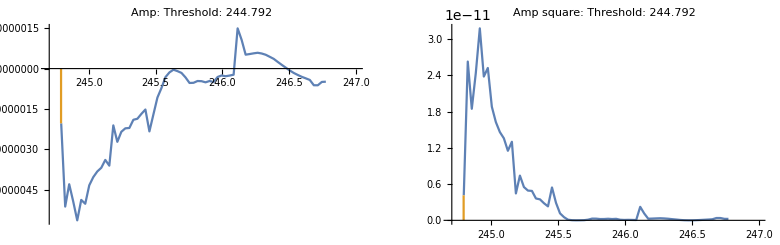

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,247},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,247},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{20,10,0,0},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=124.544  M2=122.906  M3=120.335  M4=120.335

{{124.544,122.906,120.335,120.335},{{247.451,-101.395},{247.481,-68.2881},{247.511,-38.8397},{247.541,-13.8191},{247.571,7.6165},{247.601,25.7453},{247.631,41.358},{247.661,54.536},{247.691,65.3969},{247.721,74.5176},{247.751,81.8134},{247.781,87.6384},{247.811,92.2701},{247.841,95.7512},{247.871,98.2644},{247.901,100.139},{247.931,101.028},{247.961,101.351},{247.991,101.22},{248.021,100.628},{248.051,99.711},{248.081,98.359},{248.111,96.7845},{248.141,94.9894},{248.171,93.0439},{248.201,90.9519},{248.231,88.7308},{248.261,86.4532},{248.291,84.0831},{248.321,81.6874},{248.351,79.2732},{248.381,76.8477},{248.411,74.4274},{248.441,72.0633},{248.471,69.7038},{248.501,67.3226},{248.531,65.018},{248.561,62.7631},{248.591,60.5569},{248.621,58.4149},{248.651,56.3071},{248.681,54.2714},{248.711,52.294},{248.741,50.3686},{248.771,48.5152},{248.801,46.7132},{248.831,44.9671},{248.861,43.2914},{248.891,41.6557},{248.921,40.0877},{248.951,38.5719},{248.981,37.1151},{249.011,35.7115},{249.041,34.3606},{249.071,33.0527},{249.101,31.7992},{249.131,30.5958},{249.161,29.4394},{249.191,28.3424},{249.221,27.2557},{249.251,26.2504},{249.281,25.2659},{249.311,24.321},{249.341,23.4124},{249.371,22.5415},{249.401,21.7046},{249.431,20.8997}}}

```mathematica
Msumdat[[2]]=Sort@DeleteDuplicates[Msum[60,{20,10,0,0},SRange->{10^-3,0.2,0.01},Lambda->10^-5][[2]]~Join~Msumdat[[2]]]
```

Wavefunction build complete.

M1=124.544  M2=122.906  M3=120.335  M4=120.335

{{247.451,-101.395},{247.461,-89.7615},{247.471,-78.3943},{247.481,-68.2881},{247.491,-57.8008},{247.501,-48.0228},{247.511,-38.8397},{247.521,-29.8616},{247.531,-22.0183},{247.541,-13.8191},{247.551,-6.30414},{247.561,0.781726},{247.571,7.6165},{247.581,14.0992},{247.591,20.1249},{247.601,25.7453},{247.601,25.7453},{247.611,31.3536},{247.621,36.537},{247.631,41.358},{247.641,45.9875},{247.661,54.536},{247.691,65.3969},{247.721,74.5176},{247.751,81.8134},{247.781,87.6384},{247.811,92.2701},{247.841,95.7512},{247.871,98.2644},{247.901,100.139},{247.931,101.028},{247.961,101.351},{247.991,101.22},{248.021,100.628},{248.051,99.711},{248.081,98.359},{248.111,96.7845},{248.141,94.9894},{248.171,93.0439},{248.201,90.9519},{248.231,88.7308},{248.261,86.4532},{248.291,84.0831},{248.321,81.6874},{248.351,79.2732},{248.381,76.8477},{248.411,74.4274},{248.441,72.0633},{248.471,69.7038},{248.501,67.3226},{248.531,65.018},{248.561,62.7631},{248.591,60.5569},{248.621,58.4149},{248.651,56.3071},{248.681,54.2714},{248.711,52.294},{248.741,50.3686},{248.771,48.5152},{248.801,46.7132},{248.831,44.9671},{248.861,43.2914},{248.891,41.6557},{248.921,40.0877},{248.951,38.5719},{248.981,37.1151},{249.011,35.7115},{249.041,34.3606},{249.071,33.0527},{249.101,31.7992},{249.131,30.5958},{249.161,29.4394},{249.191,28.3424},{249.221,27.2557},{249.251,26.2504},{249.281,25.2659},{249.311,24.321},{249.341,23.4124},{249.371,22.5415},{249.401,21.7046},{249.431,20.8997}}

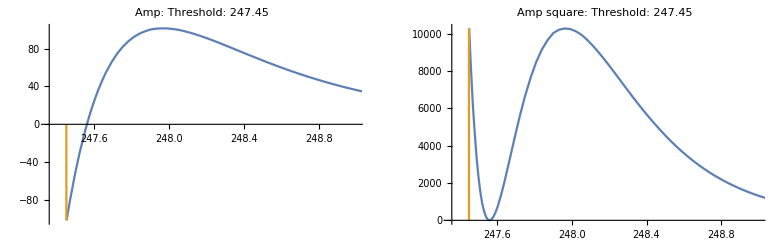

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,249},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,249},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,2,2,1},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=121.104  M4=120.79

{{121.104,121.104,121.104,120.79},{{242.208,9.85381×10^-6},{242.238,3.42884×10^-6},{242.268,1.26738×10^-6},{242.298,-1.50874×10^-7},{242.328,-3.62809×10^-7},{242.358,8.14568×10^-7},{242.388,-1.56184×10^-6},{242.418,-2.17046×10^-6},{242.448,-4.0202×10^-6},{242.478,-5.84505×10^-6},{242.508,-7.4498×10^-6},{242.538,-9.53488×10^-6},{242.568,-0.0000122495},{242.598,-0.0000148573},{242.628,-0.0000147128},{242.658,-0.0000183346},{242.688,-0.0000188854},{242.718,-0.0000205464},{242.748,-0.0000201736},{242.778,-0.0000215294},{242.808,-0.0000200353},{242.838,-0.0000213021},{242.868,-0.0000231134},{242.898,-0.0000207537},{242.928,-0.0000186047},{242.958,-0.0000214906},{242.988,-0.0000195701},{243.018,-0.0000198198},{243.048,-0.0000171503},{243.078,-0.0000183257},{243.108,-0.0000164423},{243.138,-0.0000151827},{243.168,-0.0000156086},{243.198,-0.0000130821},{243.228,-0.0000133726},{243.258,-0.0000126989},{243.288,-0.0000108947},{243.318,-0.0000110163},{243.348,-0.0000106478},{243.378,-0.0000102037},{243.408,-7.86461×10^-6},{243.438,-8.9282×10^-6},{243.468,-7.57318×10^-6},{243.498,-6.95751×10^-6},{243.528,-6.52197×10^-6},{243.558,-6.51957×10^-6},{243.588,-5.59482×10^-6},{243.618,-4.57207×10^-6},{243.648,-4.34971×10^-6},{243.678,-4.19208×10^-6},{243.708,-3.7756×10^-6},{243.738,-3.40856×10^-6},{243.768,-3.12486×10^-6},{243.798,-3.21539×10^-6},{243.828,-2.84546×10^-6},{243.858,-2.54715×10^-6},{243.888,-2.17814×10^-6},{243.918,-1.93082×10^-6},{243.948,-1.64182×10^-6},{243.978,-1.57923×10^-6},{244.008,-1.43415×10^-6},{244.038,-6.60676×10^-7},{244.068,2.2752×10^-7},{244.098,-1.01982×10^-6},{244.128,-7.27427×10^-7},{244.158,-6.85596×10^-7},{244.188,-6.00227×10^-7}}}

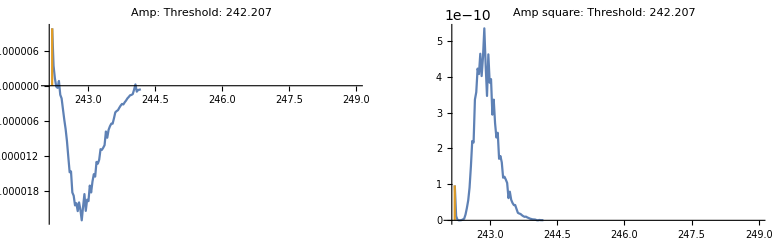

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,249},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,249},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,2,2,2},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=121.104  M4=121.104

{{121.104,121.104,121.104,121.104},{{242.208,-6484.36},{242.238,-7357.1},{242.268,-6895.85},{242.298,-6069.43},{242.328,-5318.48},{242.358,-4792.04},{242.388,-4499.01},{242.418,-4386.41},{242.448,-4377.6},{242.478,-4424.39},{242.508,-4483.5},{242.538,-4494.},{242.568,-4375.85},{242.598,-4348.73},{242.628,-4131.76},{242.658,-3983.77},{242.688,-3743.17},{242.718,-3474.83},{242.748,-3194.66},{242.778,-2912.18},{242.808,-2635.12},{242.838,-2377.78},{242.868,-2138.02},{242.898,-1922.07},{242.928,-1731.72},{242.958,-1568.03},{242.988,-1456.87},{243.018,-1317.68},{243.048,-1228.69},{243.078,-1169.7},{243.108,-1112.03},{243.138,-1078.66},{243.168,-1060.29},{243.198,-1053.15},{243.228,-1055.85},{243.258,-1075.79},{243.288,-1090.07},{243.318,-1105.3},{243.348,-1131.82},{243.378,-1142.9},{243.408,-1165.73},{243.438,-1188.04},{243.468,-1209.19},{243.498,-1228.38},{243.528,-1245.9},{243.558,-1260.4},{243.588,-1272.86},{243.618,-1282.28},{243.648,-1289.1},{243.678,-1293.28},{243.708,-1294.79},{243.738,-1285.12},{243.768,-1290.49},{243.798,-1285.01},{243.828,-1277.56},{243.858,-1268.22},{243.888,-1256.65},{243.918,-1244.43},{243.948,-1230.65},{243.978,-1215.24},{244.008,-1199.09},{244.038,-1182.02},{244.068,-1164.24},{244.098,-1145.89},{244.128,-1127.03},{244.158,-1107.86},{244.188,-1088.3}}}

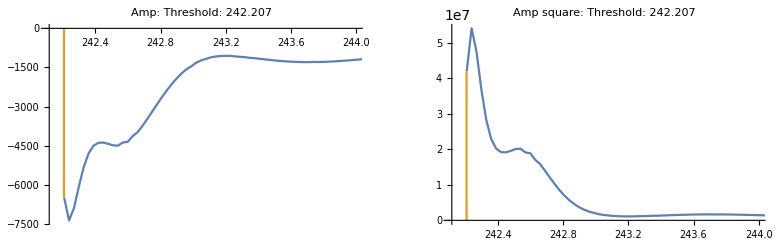

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,1,2,1},SRange->{10^-3,0.5,0.01},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=120.79  M3=121.104  M4=120.79

{{121.104,120.79,121.104,120.79},{{241.895,-5071.45},{241.905,-4752.58},{241.915,-4539.5},{241.925,-4385.77},{241.935,-4082.39},{241.945,-4302.27},{241.955,-4315.95},{241.965,-4353.88},{241.975,-4446.84},{241.985,-4507.},{241.995,-4568.27},{242.005,-4625.01},{242.015,-4675.39},{242.025,-4715.2},{242.035,-4742.61},{242.045,-4758.54},{242.055,-4760.25},{242.065,-4748.28},{242.075,-4724.29},{242.085,-4686.5},{242.095,-4635.73},{242.105,-4574.21},{242.115,-4502.56},{242.125,-4424.84},{242.135,-4258.56},{242.145,1.5681×10^6},{242.155,-4132.5},{242.165,-4024.69},{242.175,-3912.35},{242.185,-3796.8},{242.195,-3679.44},{242.205,-3559.28},{242.215,-3439.12},{242.225,-3329.6},{242.235,-3210.97},{242.245,-3081.44},{242.255,-2977.74},{242.265,-2864.23},{242.275,-2753.59},{242.285,-2645.67},{242.295,-2542.35},{242.305,-2440.37},{242.315,-2345.54},{242.325,-2251.73},{242.335,-2163.44},{242.345,-2079.36},{242.355,-1999.58},{242.365,-1924.16},{242.375,-1853.28},{242.385,-1786.42}}}

```mathematica
Msumdat[[2]]=Msumdat[[2]]~Join~Msum[60,{2,1,2,1},SRange->{0.5+10^-3,2,0.03},Lambda->10^-5][[2]]
```

Wavefunction build complete.

M1=121.104  M2=120.79  M3=121.104  M4=120.79

{{241.895,-5071.45},{241.905,-4752.58},{241.915,-4539.5},{241.925,-4385.77},{241.935,-4082.39},{241.945,-4302.27},{241.955,-4315.95},{241.965,-4353.88},{241.975,-4446.84},{241.985,-4507.},{241.995,-4568.27},{242.005,-4625.01},{242.015,-4675.39},{242.025,-4715.2},{242.035,-4742.61},{242.045,-4758.54},{242.055,-4760.25},{242.065,-4748.28},{242.075,-4724.29},{242.085,-4686.5},{242.095,-4635.73},{242.105,-4574.21},{242.115,-4502.56},{242.125,-4424.84},{242.135,-4258.56},{242.145,1.5681×10^6},{242.155,-4132.5},{242.165,-4024.69},{242.175,-3912.35},{242.185,-3796.8},{242.195,-3679.44},{242.205,-3559.28},{242.215,-3439.12},{242.225,-3329.6},{242.235,-3210.97},{242.245,-3081.44},{242.255,-2977.74},{242.265,-2864.23},{242.275,-2753.59},{242.285,-2645.67},{242.295,-2542.35},{242.305,-2440.37},{242.315,-2345.54},{242.325,-2251.73},{242.335,-2163.44},{242.345,-2079.36},{242.355,-1999.58},{242.365,-1924.16},{242.375,-1853.28},{242.385,-1786.42},{242.395,-1724.19},{242.425,-1563.32},{242.455,-1437.91},{242.485,-1342.16},{242.515,-1268.88},{242.545,-1230.43},{242.575,-1211.61},{242.605,-1209.58},{242.635,-1219.14},{242.665,-1205.44},{242.695,-1270.37},{242.725,-1299.84},{242.755,-1335.43},{242.785,-1367.34},{242.815,-1398.23},{242.845,-1389.38},{242.875,-1423.57},{242.905,-1451.25},{242.935,-1425.47},{242.965,-1489.58},{242.995,-1521.},{243.025,-1510.82},{243.055,-1518.61},{243.085,-1532.75},{243.115,-1529.49},{243.145,-1522.98},{243.175,-1513.51},{243.205,-1501.35},{243.235,-1487.21},{243.265,-1471.18},{243.295,-1453.78},{243.325,-1433.45},{243.355,-1411.82},{243.385,-1385.7},{243.415,-1358.52},{243.445,-1337.36},{243.475,-1311.95},{243.505,-1286.82},{243.535,-1259.59},{243.565,-1237.31},{243.595,-1211.43},{243.625,-1185.69},{243.655,-1160.67},{243.685,-1135.33},{243.715,-1110.32},{243.745,-1085.66},{243.775,-1061.43},{243.805,-1037.63},{243.835,-1013.98},{243.865,-658.591}}

```mathematica
Msumdat[[2]]=Msumdat[[2]]~Join~Msum[60,{2,1,2,1},SRange->{2+10^-3,2.5,0.03},Lambda->10^-5][[2]]
```

Wavefunction build complete.

M1=121.104  M2=120.79  M3=121.104  M4=120.79

{{241.895,-5071.45},{241.905,-4752.58},{241.915,-4539.5},{241.925,-4385.77},{241.935,-4082.39},{241.945,-4302.27},{241.955,-4315.95},{241.965,-4353.88},{241.975,-4446.84},{241.985,-4507.},{241.995,-4568.27},{242.005,-4625.01},{242.015,-4675.39},{242.025,-4715.2},{242.035,-4742.61},{242.045,-4758.54},{242.055,-4760.25},{242.065,-4748.28},{242.075,-4724.29},{242.085,-4686.5},{242.095,-4635.73},{242.105,-4574.21},{242.115,-4502.56},{242.125,-4424.84},{242.135,-4258.56},{242.145,1.5681×10^6},{242.155,-4132.5},{242.165,-4024.69},{242.175,-3912.35},{242.185,-3796.8},{242.195,-3679.44},{242.205,-3559.28},{242.215,-3439.12},{242.225,-3329.6},{242.235,-3210.97},{242.245,-3081.44},{242.255,-2977.74},{242.265,-2864.23},{242.275,-2753.59},{242.285,-2645.67},{242.295,-2542.35},{242.305,-2440.37},{242.315,-2345.54},{242.325,-2251.73},{242.335,-2163.44},{242.345,-2079.36},{242.355,-1999.58},{242.365,-1924.16},{242.375,-1853.28},{242.385,-1786.42},{242.395,-1724.19},{242.425,-1563.32},{242.455,-1437.91},{242.485,-1342.16},{242.515,-1268.88},{242.545,-1230.43},{242.575,-1211.61},{242.605,-1209.58},{242.635,-1219.14},{242.665,-1205.44},{242.695,-1270.37},{242.725,-1299.84},{242.755,-1335.43},{242.785,-1367.34},{242.815,-1398.23},{242.845,-1389.38},{242.875,-1423.57},{242.905,-1451.25},{242.935,-1425.47},{242.965,-1489.58},{242.995,-1521.},{243.025,-1510.82},{243.055,-1518.61},{243.085,-1532.75},{243.115,-1529.49},{243.145,-1522.98},{243.175,-1513.51},{243.205,-1501.35},{243.235,-1487.21},{243.265,-1471.18},{243.295,-1453.78},{243.325,-1433.45},{243.355,-1411.82},{243.385,-1385.7},{243.415,-1358.52},{243.445,-1337.36},{243.475,-1311.95},{243.505,-1286.82},{243.535,-1259.59},{243.565,-1237.31},{243.595,-1211.43},{243.625,-1185.69},{243.655,-1160.67},{243.685,-1135.33},{243.715,-1110.32},{243.745,-1085.66},{243.775,-1061.43},{243.805,-1037.63},{243.835,-1013.98},{243.865,-658.591},{243.895,-969.191},{243.925,-947.435},{243.955,-926.223},{243.985,-905.569},{244.015,-885.47},{244.045,-865.93},{244.075,-846.935},{244.105,-828.492},{244.135,-810.145},{244.165,-792.814},{244.195,-776.008},{244.225,-760.043},{244.255,-744.217},{244.285,-728.865},{244.315,-713.708},{244.345,-699.056},{244.375,-685.63}}

```mathematica
Msumdat[[2]]=Delete[Msumdat[[2]],5];
```

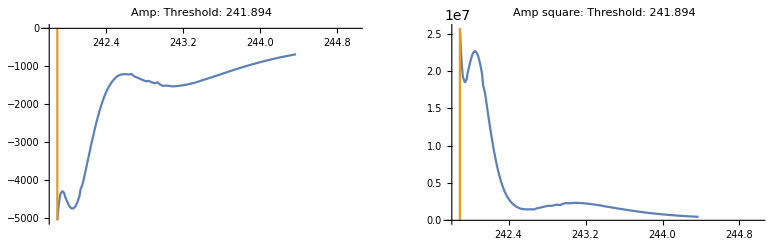

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,245},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,245},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,2,1,1},SRange->{10^-3,2,0.03},Lambda->10^-4.9]
```

Wavefunction build complete.

M1=121.104  M2=121.104  M3=120.79  M4=120.79

{{121.104,121.104,120.79,120.79},{{242.208,4390.68},{242.238,3770.08},{242.268,3181.25},{242.298,2642.19},{242.328,2145.11},{242.358,1743.44},{242.388,1409.27},{242.418,1137.18},{242.448,923.823},{242.478,886.987},{242.508,657.18},{242.538,154.625},{242.568,531.932},{242.598,511.687},{242.628,511.736},{242.658,528.166},{242.688,634.398},{242.718,648.837},{242.748,688.415},{242.778,722.003},{242.808,756.972},{242.838,792.155},{242.868,826.047},{242.898,857.619},{242.928,886.379},{242.958,901.816},{242.988,927.118},{243.018,948.005},{243.048,964.572},{243.078,976.862},{243.108,985.299},{243.138,989.918},{243.168,877.502},{243.198,884.691},{243.228,888.315},{243.258,887.265},{243.288,886.231},{243.318,881.121},{243.348,873.676},{243.378,856.316},{243.408,845.226},{243.438,840.478},{243.468,826.599},{243.498,812.289},{243.528,795.804},{243.558,779.296},{243.588,762.256},{243.618,744.843},{243.648,727.142},{243.678,709.28},{243.708,691.4},{243.738,673.552},{243.768,655.731},{243.798,638.114},{243.828,620.706},{243.858,603.561},{243.888,587.208},{243.918,570.684},{243.948,554.515},{243.978,538.715},{244.008,523.301},{244.038,498.197},{244.068,468.208},{244.098,456.196},{244.128,459.786},{244.158,446.914},{244.188,439.328}}}

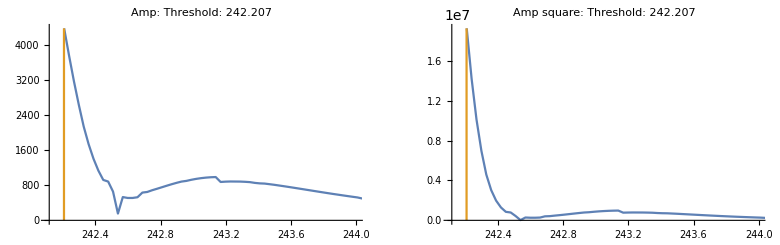

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[60,{2,1,1,1},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=121.104  M2=120.79  M3=120.79  M4=120.79

{{121.104,120.79,120.79,120.79},{{241.895,9.94325×10^-6},{241.925,7.86578×10^-6},{241.955,7.30525×10^-6},{241.985,0.0000100292},{242.015,0.0000132089},{242.045,0.0000167321},{242.075,0.000018819},{242.105,0.0000220279},{242.135,0.0000258339},{242.165,0.0000250602},{242.195,0.0000280824},{242.225,0.0000269284},{242.255,0.0000305272},{242.285,0.0000297702},{242.315,0.0000291813},{242.345,0.000027597},{242.375,0.0000273753},{242.405,0.0000274857},{242.435,0.0000258531},{242.465,0.0000249935},{242.495,0.0000249426},{242.525,0.0000205365},{242.555,0.0000201692},{242.585,0.0000188147},{242.615,0.0000183729},{242.645,0.0000160024},{242.675,0.0000160276},{242.705,0.0000153672},{242.735,0.0000144797},{242.765,0.000012133},{242.795,0.0000114832},{242.825,0.0000107445},{242.855,9.2001×10^-6},{242.885,8.91718×10^-6},{242.915,8.03878×10^-6},{242.945,7.14756×10^-6},{242.975,6.636×10^-6},{243.005,6.33301×10^-6},{243.035,6.13415×10^-6},{243.065,5.19303×10^-6},{243.095,5.12451×10^-6},{243.125,4.38103×10^-6},{243.155,3.76692×10^-6},{243.185,3.61021×10^-6},{243.215,3.1371×10^-6},{243.245,2.87694×10^-6},{243.275,2.62939×10^-6},{243.305,2.54325×10^-6},{243.335,2.19216×10^-6},{243.365,2.09946×10^-6},{243.395,1.98387×10^-6},{243.425,1.71689×10^-6},{243.455,1.56763×10^-6},{243.485,1.40928×10^-6},{243.515,1.30616×10^-6},{243.545,1.09619×10^-6},{243.575,9.846×10^-7},{243.605,9.67544×10^-7},{243.635,8.93886×10^-7},{243.665,8.97316×10^-7},{243.695,8.48305×10^-7},{243.725,8.77484×10^-7},{243.755,5.64132×10^-7},{243.785,5.87794×10^-7},{243.815,4.80163×10^-7},{243.845,4.00618×10^-7},{243.875,3.38408×10^-7}}}

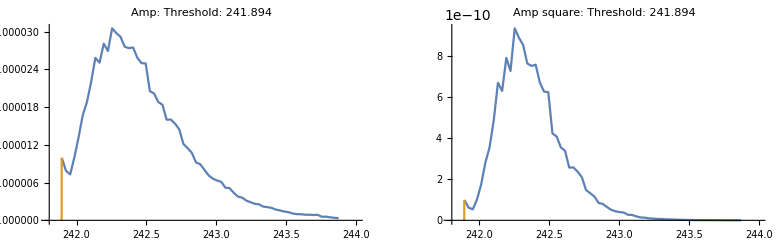

```mathematica
GraphicsGrid[{{ListPlot[{Select[Re@Msumdat[[2]],#∈Reals&],{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],First[Msumdat[[2]]][[2]]}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium],
ListPlot[{Transpose@{Transpose[Msumdat[[2]]][[1]],(Transpose[Msumdat[[2]]][[2]])^2},{{Msumdat[[1,1]]+Msumdat[[1,2]],0},{Msumdat[[1,1]]+Msumdat[[1,2]],(First[Msumdat[[2]]][[2]])^2}}},PlotRange->{{Msumdat[[1,1]]+Msumdat[[1,2]]-0.1,244},All},Joined->True,PlotLabel->"Amp square: Threshold: "<>ToString[Msumdat[[1,1]]+Msumdat[[1,2]]],ImageSize->Medium]}}]
```

```mathematica
Msumdat=Msum[100,{0,0,1,1},SRange->{0.001,1.5,0.01},Lambda->10^-7]
```

Wavefunction build complete.

M1=200.287  M2=200.287  M3=200.67  M4=200.67

{{{0,0,1,1},{200.287,200.287,200.67,200.67}},{{401.342,592.776},{401.362,947.256},{401.382,1310.18},{401.402,1481.7},{401.422,1607.46},{401.442,1732.74},{401.462,17885.3},{401.482,2009.69},{401.502,2037.89},{401.522,2093.55},{401.542,2138.7},{401.562,2181.62},{401.582,2203.19},{401.602,9885.41},{401.622,2226.48},{401.642,2123.39},{401.662,2177.68},{401.682,2344.32},{401.702,2353.56},{401.722,2130.32},{401.742,2106.21},{401.762,2071.42},{401.782,2043.4},{401.802,2014.86},{401.822,1980.32},{401.842,1900.45},{401.862,1932.5},{401.882,1860.9},{401.902,1823.85},{401.922,1766.58},{401.942,1742.76},{401.962,1711.13},{401.982,1663.99},{402.002,1623.29},{402.022,1590.33},{402.042,1558.31},{402.062,1523.02},{402.082,1473.5},{402.102,1435.52},{402.122,1397.22},{402.142,1360.42},{402.162,1323.76},{402.182,1286.19},{402.202,1251.81},{402.222,1216.67},{402.242,1181.99},{402.262,1148.04},{402.282,1114.74},{402.302,1081.96},{402.322,1013.35},{402.342,979.567},{402.362,991.597},{402.382,959.78},{402.402,929.17},{402.422,899.892},{402.442,869.24},{402.462,844.598},{402.482,817.74},{402.502,791.353},{402.522,765.711},{402.542,740.644},{402.562,716.346},{402.582,692.463},{402.602,626.85},{402.622,611.209},{402.642,595.222},{402.662,580.149},{402.682,565.831},{402.702,552.1},{402.722,540.029},{402.742,525.378},{402.762,513.038},{402.782,501.115},{402.802,489.126},{402.822,477.604},{402.842,466.358},{402.862,465.65},{402.882,457.769},{402.902,447.926},{402.922,438.392},{402.942,429.166},{402.962,420.233},{402.982,411.562},{403.002,403.535},{403.022,395.402},{403.042,387.191},{403.062,379.733},{403.082,372.345},{403.102,365.085},{403.122,354.393},{403.142,347.408},{403.162,340.628},{403.182,334.032},{403.202,327.819},{403.222,321.62},{403.242,315.325},{403.262,309.419},{403.282,303.665},{403.302,298.075},{403.322,292.632}}}

```mathematica
Msumdat[[2]]=Delete[Msumdat[[2]],13];
```

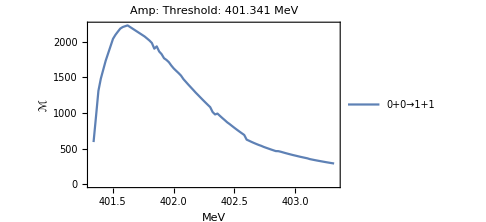
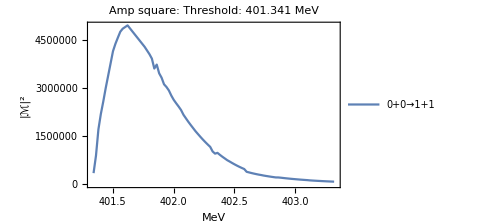

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,0.1},Joined->,LegendMargins->],displayfunction2[Msumdat,{-0.1,0.1},Joined-> ,LegendMargins->]}]
```

```mathematica
Msumdat=Msum[100,{0,0,1,0},SRange->{0.001,2,0.01},Lambda->10^-6]
```

Wavefunction build complete.

M1=200.287  M2=200.287  M3=200.67  M4=200.287

{{{0,0,1,0},{200.287,200.287,200.67,200.287}},{{400.958,0.000867482},{400.968,-0.000260888},{400.978,-0.000357875},{400.988,-0.00108363},{400.998,-0.00129308},{401.008,-0.00197166},{401.018,-0.00192014},{401.028,-0.00232165},{401.038,-0.00196806},{401.048,-0.00186059},{401.058,-0.00240885},{401.068,-0.00242969},{401.078,-0.00204415},{401.088,-0.00200344},{401.098,-0.0021403},{401.108,-0.00218231},{401.118,-0.00201925},{401.128,-0.00174274},{401.138,-0.00202873},{401.148,-0.00197898},{401.158,-0.00183477},{401.168,-0.00195562},{401.178,-0.00191224},{401.188,-0.00147659},{401.198,-0.00174104},{401.208,-0.00173769},{401.218,-0.00154517},{401.228,-0.00159453},{401.238,-0.00143523},{401.248,-0.00139576},{401.258,-0.00139167},{401.268,-0.00130684},{401.278,-0.00127717},{401.288,-0.00126294},{401.298,-0.00118405},{401.308,-0.00109747},{401.318,-0.00103561},{401.328,-0.000999051},{401.338,-0.0010214},{401.348,-0.000934692},{401.358,-0.000948868},{401.368,-0.000838795},{401.378,-0.000801974},{401.388,-0.000833011},{401.398,-0.0008156},{401.408,-0.000758829},{401.418,-0.000760266},{401.428,-0.000669364},{401.438,-0.000615123},{401.448,-0.00335685},{401.458,-0.000560629},{401.468,-0.000591829},{401.478,-0.000551741},{401.488,-0.000555929},{401.498,-0.000496414},{401.508,-0.00048102},{401.518,-0.00048249},{401.528,-0.00044545},{401.538,-0.000442841},{401.548,-0.00040113},{401.558,-0.00038132},{401.568,-0.00039553},{401.578,-0.000358455},{401.588,-0.000326228},{401.598,-0.000348716},{401.608,-0.000325395},{401.618,-0.00028607},{401.628,-0.000279197},{401.638,-0.000287539},{401.648,-0.000274624},{401.658,-0.000264753},{401.668,-0.000250174},{401.678,-0.000246952},{401.688,-0.000232714},{401.698,-0.000227072},{401.708,-0.000213324},{401.718,-0.000207729},{401.728,-0.000205136},{401.738,-0.000191302},{401.748,-0.00017876},{401.758,-0.000162457},{401.768,-0.000156773},{401.778,-0.000177203},{401.788,-0.000129966},{401.798,-0.000127023},{401.808,-0.000143899},{401.818,-0.000124471},{401.828,-0.000122258},{401.838,-0.000122791},{401.848,-0.000122601},{401.858,-0.000111521},{401.868,-0.000113328},{401.878,-0.0000976795},{401.888,-0.000109119},{401.898,-0.000102957},{401.908,-0.0000940669},{401.918,-0.0000928152},{401.928,-0.0000922143},{401.938,-0.0000881968},{401.948,-0.0000875477},{401.958,-0.0000887585},{401.968,-0.0000880671},{401.978,-0.0000791829},{401.988,-0.0000737192},{401.998,-0.0000637662},{402.008,-0.0000697487},{402.018,-0.0000628778},{402.028,-0.0000624099},{402.038,-0.0000563732},{402.048,-0.0000325737},{402.058,-0.0000294549},{402.068,-0.0000301587},{402.078,-0.00004685},{402.088,-0.0000475611},{402.098,-0.0000517603},{402.108,-0.0000427381},{402.118,-0.0000438648},{402.128,-0.0000398577},{402.138,-0.0000412983},{402.148,-0.0000392893},{402.158,-0.0000376755},{402.168,-0.0000329527},{402.178,-0.0000358065},{402.188,-0.0000310099},{402.198,-0.0000307034},{402.208,-0.0000307326},{402.218,-0.0000284521},{402.228,-0.0000270724},{402.238,-0.0000259043},{402.248,-0.0000218633},{402.258,-0.0000241652},{402.268,-0.000024991},{402.278,-0.0000232886},{402.288,-0.0000207832},{402.298,-0.0000212398},{402.308,-0.0000259863},{402.318,-0.0000196683},{402.328,-0.0000175679},{402.338,-0.000017906},{402.348,-0.0000188074},{402.358,-0.0000198421},{402.368,-0.0000189921},{402.378,-0.0000192116},{402.388,-0.0000167463},{402.398,-0.000016276},{402.408,-0.0000164908},{402.418,-0.0000179526},{402.428,-0.0000171326},{402.438,-0.0000158944},{402.448,-0.0000141461},{402.458,-0.0000345069},{402.468,-0.0000339905},{402.478,-8.29283×10^-6},{402.488,-0.000011542},{402.498,-0.000011349},{402.508,-0.0000109913},{402.518,-0.0000349214},{402.528,-0.0000101227},{402.538,-8.65684×10^-6},{402.548,-9.2877×10^-6},{402.558,-8.95594×10^-6},{402.568,-8.57997×10^-6},{402.578,-7.69874×10^-6},{402.588,-7.99012×10^-6},{402.598,-7.13871×10^-6},{402.608,-7.50465×10^-6},{402.618,-6.67668×10^-6},{402.628,-6.80971×10^-6},{402.638,-6.94593×10^-6},{402.648,-6.34832×10^-6},{402.658,-6.62241×10^-6},{402.668,-6.0307×10^-6},{402.678,-6.10043×10^-6},{402.688,-5.57715×10^-6},{402.698,-5.73934×10^-6},{402.708,-5.37202×10^-6},{402.718,-5.2023×10^-6},{402.728,-5.24367×10^-6},{402.738,-4.96887×10^-6},{402.748,-4.34983×10^-6},{402.758,-4.18283×10^-6},{402.768,-3.97393×10^-6},{402.778,-4.01289×10^-6},{402.788,-3.76508×10^-6},{402.798,-4.04782×10^-6},{402.808,-3.35275×10^-6},{402.818,-3.42668×10^-6},{402.828,-3.24788×10^-6},{402.838,-3.22931×10^-6},{402.848,-2.96238×10^-6},{402.858,-3.05269×10^-6},{402.868,-2.79767×10^-6},{402.878,-4.98539×10^-6},{402.888,-4.78716×10^-6},{402.898,-4.71963×10^-6},{402.908,-2.72052×10^-6},{402.918,-2.85089×10^-6},{402.928,-2.78682×10^-6},{402.938,-2.63187×10^-6},{402.948,-2.64611×10^-6}}}

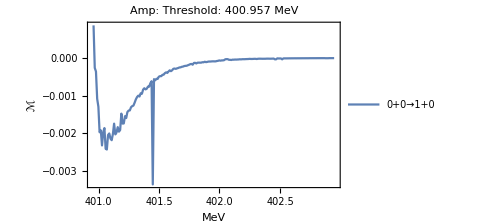
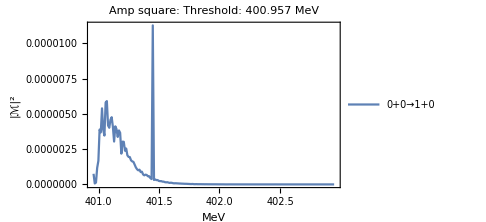

```mathematica
Row[{displayfunction1[Msumdat,{-0.01,0.01},Joined->,LegendMargins->],displayfunction2[Msumdat,{-0.01,0.01},Joined-> ,LegendMargins->]}]
```

```mathematica
Msum[90,{0,0,1,1},SRange->{10^-3+0.07,10^-3+0.07,0.1},Lambda->10^-6]
```

Wavefunction build complete.

M1=180.296  M2=180.296  M3=180.694  M4=180.694

{{{0,0,1,1},{180.296,180.296,180.694,180.694}},{{361.458,1203.94}}}

```mathematica
Msumdat=Msum[90,{0,0,1,1},SRange->{10^-3,2,0.01},Lambda->10^-5]
```

Wavefunction build complete.

M1=180.296  M2=180.296  M3=180.694  M4=180.694

{{{0,0,1,1},{180.296,180.296,180.694,180.694}},{{361.388,583.224},{361.398,694.403},{361.408,797.724},{361.418,894.716},{361.428,983.343},{361.438,1065.71},{361.448,1141.77},{361.458,810.013},{361.468,1276.85},{361.478,1336.05},{361.488,1391.75},{361.498,1439.31},{361.508,1485.29},{361.518,1525.74},{361.528,1561.96},{361.538,1588.65},{361.548,1619.73},{361.558,1642.96},{361.568,1664.75},{361.578,1684.77},{361.588,1701.37},{361.598,1715.28},{361.608,1726.81},{361.618,1735.94},{361.628,1748.44},{361.638,1751.38},{361.648,1756.63},{361.658,1758.98},{361.668,1758.53},{361.678,1757.18},{361.688,1754.41},{361.698,1750.32},{361.708,1745.39},{361.718,1738.56},{361.728,1731.26},{361.738,1722.87},{361.748,1703.81},{361.758,1703.19},{361.768,1692.47},{361.778,1680.5},{361.788,1668.79},{361.798,1656.16},{361.808,1651.08},{361.818,1636.86},{361.828,1622.66},{361.838,1608.},{361.848,1593.08},{361.858,1577.71},{361.868,1562.12},{361.878,1546.36},{361.888,1530.05},{361.898,1513.9},{361.908,1497.6},{361.918,1481.33},{361.928,1464.79},{361.938,1448.2},{361.948,1431.55},{361.958,1415.7},{361.968,1398.19},{361.978,1381.78},{361.988,1365.13},{361.998,1348.6},{362.008,1332.04},{362.018,1315.53},{362.028,1299.11},{362.038,1281.97},{362.048,1265.53},{362.058,1249.34},{362.068,1233.26},{362.078,1217.3},{362.088,1201.97},{362.098,1189.26},{362.108,1173.83},{362.118,1159.08},{362.128,1144.21},{362.138,1129.54},{362.148,1114.74},{362.158,1100.08},{362.168,1085.6},{362.178,1071.28},{362.188,1057.13},{362.198,1043.14},{362.208,1029.33},{362.218,1015.68},{362.228,1002.21},{362.238,988.917},{362.248,975.793},{362.258,962.928},{362.268,950.23},{362.278,937.61},{362.288,925.195},{362.298,912.936},{362.308,900.855},{362.318,888.938},{362.328,877.191},{362.338,865.615},{362.348,854.201},{362.358,842.966},{362.368,831.87},{362.378,820.953},{362.388,810.21},{362.398,799.613},{362.408,789.305},{362.418,779.067},{362.428,768.947},{362.438,759.028},{362.448,749.215},{362.458,739.55},{362.468,730.033},{362.478,720.664},{362.488,711.439},{362.498,702.33},{362.508,693.39},{362.518,684.616},{362.528,675.924},{362.538,667.395},{362.548,659.},{362.558,650.736},{362.568,642.601},{362.578,634.593},{362.588,626.716},{362.598,618.96},{362.608,611.332},{362.618,603.807},{362.628,596.41},{362.638,589.127},{362.648,581.965},{362.658,574.88},{362.668,567.912},{362.678,561.127},{362.688,554.398},{362.698,547.745},{362.708,541.224},{362.718,534.735},{362.728,528.485},{362.738,522.198},{362.748,516.073},{362.758,510.038},{362.768,504.112},{362.778,498.269},{362.788,492.538},{362.798,486.924},{362.808,481.338},{362.818,475.847},{362.828,470.44},{362.838,465.132},{362.848,459.888},{362.858,454.722},{362.868,449.639},{362.878,444.632},{362.888,439.702},{362.898,434.845},{362.908,430.061},{362.918,425.35},{362.928,420.71},{362.938,416.151},{362.948,411.649},{362.958,407.214},{362.968,402.844},{362.978,398.54},{362.988,394.299},{362.998,390.122},{363.008,386.006},{363.018,381.949},{363.028,377.952},{363.038,374.015},{363.048,370.133},{363.058,366.308},{363.068,362.539},{363.078,358.824},{363.088,355.163},{363.098,351.555},{363.108,347.999},{363.118,344.493},{363.128,341.037},{363.138,337.63},{363.148,334.271},{363.158,330.959},{363.168,327.693},{363.178,324.474},{363.188,321.3},{363.198,318.172},{363.208,315.085},{363.218,312.042},{363.228,309.04},{363.238,306.081},{363.248,303.161},{363.258,300.281},{363.268,297.441},{363.278,294.639},{363.288,291.875},{363.298,289.148},{363.308,286.458},{363.318,283.803},{363.328,281.183},{363.338,278.599},{363.348,276.05},{363.358,273.534},{363.368,271.051},{363.378,268.601}}}

```mathematica
(*DynamicSetting[DynamicModule[{x},SetterBar[Dynamic[x],{True,False}]]]*)
```

```mathematica
(*DynamicSetting[InputField[,FieldSize->1]]*)
```

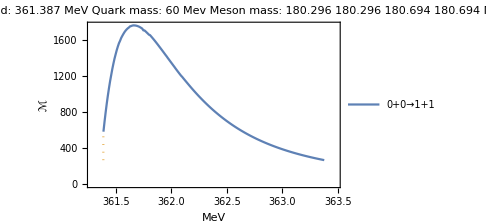
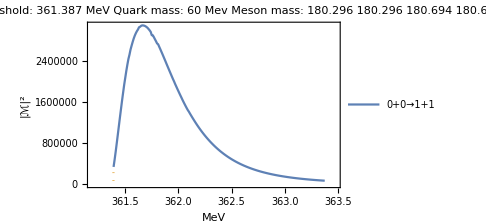

```mathematica
Row[{displayfunction1[Msumdat,{-0.1,0.1},Joined->,LegendMargins->,ImageSize->Medium],displayfunction2[Msumdat,{-0.2,0.1},Joined-> ,LegendMargins->,ImageSize->Medium]}]
```

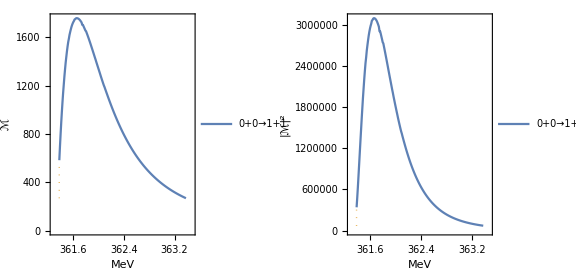

```mathematica
displayfunctionboth[Msumdat,{-0.1,0.1},Joined->,LegendMargins->,ImageSize->Large]
```

```mathematica
Get["OneFlavour`"];
```

```mathematica
Msum[60,{0,0,1,1},SRange->{10^-3,2,0.03},Lambda->10^-6]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.79  M4=120.79

{{{0,0,1,1},{120.335,120.335,120.79,120.79},{60}},{{241.581,320.915},{241.611,470.799},{241.641,559.375},{241.671,737.262},{241.701,823.158},{241.731,888.085},{241.761,922.664},{241.791,1005.73},{241.821,1013.25},{241.851,1016.74},{241.881,1027.99},{241.911,1031.52},{241.941,1024.48},{241.971,1015.23},{242.001,1000.96},{242.031,983.861},{242.061,964.738},{242.091,943.155},{242.121,920.113},{242.151,896.552},{242.181,871.313},{242.211,846.021},{242.241,820.652},{242.271,795.76},{242.301,769.78},{242.331,744.746},{242.361,720.467},{242.391,697.879},{242.421,674.227},{242.451,651.754},{242.481,629.638},{242.511,608.775},{242.541,587.899},{242.571,568.21},{242.601,548.906},{242.631,743.376},{242.661,516.117},{242.691,494.877},{242.721,478.228},{242.751,462.307},{242.781,446.963},{242.811,430.933},{242.841,416.652},{242.871,403.029},{242.901,389.789},{242.931,377.162},{242.961,365.052},{242.991,353.426},{243.021,342.262},{243.051,331.572},{243.081,321.282},{243.111,311.425},{243.141,301.955},{243.171,292.876},{243.201,284.154},{243.231,275.773},{243.261,267.725},{243.291,260.038},{243.321,252.575},{243.351,245.44},{243.381,238.575},{243.411,231.97},{243.441,225.619},{243.471,219.536},{243.501,213.689},{243.531,208.036},{243.561,202.589}}}

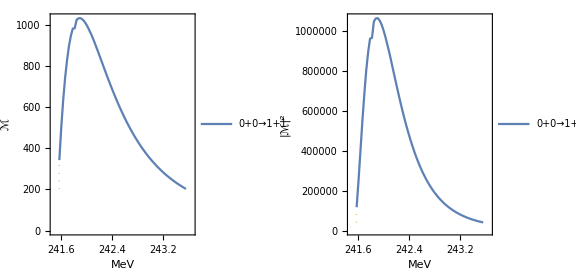

```mathematica
displayfunctionboth[Msumdat,{-0.1,0.1},Joined->,LegendMargins->,ImageSize->Large]
```

```mathematica
Msum[60,{0,0,1,1},SRange->{10^-3,2,0.03},Lambda->10^-6,I1Option->{MaxRecursion->200,Method->"LocalAdaptive"}]
```

Wavefunction build complete.

M1=120.335  M2=120.335  M3=120.79  M4=120.79

{{{0,0,1,1},{120.335,120.335,120.79,120.79},{60}},{{241.581,320.915},{241.611,470.799},{241.641,559.375},{241.671,737.262},{241.701,823.158},{241.731,888.085},{241.761,922.664},{241.791,1005.73},{241.821,1013.25},{241.851,1016.74},{241.881,1027.99},{241.911,1031.52},{241.941,1024.48},{241.971,1015.23},{242.001,1000.96},{242.031,983.861},{242.061,964.738},{242.091,943.155},{242.121,920.113},{242.151,896.552},{242.181,871.313},{242.211,846.021},{242.241,820.652},{242.271,795.76},{242.301,769.78},{242.331,744.746},{242.361,720.467},{242.391,697.879},{242.421,674.227},{242.451,651.754},{242.481,629.638},{242.511,608.775},{242.541,587.899},{242.571,568.21},{242.601,548.906},{242.631,743.376},{242.661,516.117},{242.691,494.877},{242.721,478.228},{242.751,462.307},{242.781,446.963},{242.811,430.933},{242.841,416.652},{242.871,403.029},{242.901,389.789},{242.931,377.162},{242.961,365.052},{242.991,353.426},{243.021,342.262},{243.051,331.572},{243.081,321.282},{243.111,311.425},{243.141,301.955},{243.171,292.876},{243.201,284.154},{243.231,275.773},{243.261,267.725},{243.291,260.038},{243.321,252.575},{243.351,245.44},{243.381,238.575},{243.411,231.97},{243.441,225.619},{243.471,219.536},{243.501,213.689},{243.531,208.036},{243.561,202.589}}}

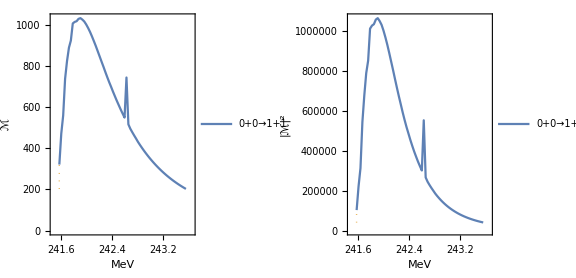

```mathematica
displayfunctionboth[%13,{-0.1,0.1},Joined->,LegendMargins->,ImageSize->Large]
```

```mathematica
Msum2[{60,80},{0,0,1,1},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=140.322  M2=140.322  M3=140.757  M4=140.757

NIntegrate::ilim: Invalid integration variable or limit(s) in {}.

General::stop: Further output of NIntegrate::ilim will be suppressed during this calculation.

{{{0,0,1,1},{140.322,140.322,140.757,140.757},{60,80}},{{281.515,3.67583 NIntegrate[1/(1+6)^2,{OneFlavour`Private`x,0,1},{OneFlavour`Private`y,0,1},FilterRules[{{}},Options[NIntegrate]]]+3.67583 1},66}}
 |  |  |  |

```mathematica
Msum3[{60,80,60},{0,0,1,1},SRange->{10^-3,2,0.03},Lambda->10^-5]
```

Wavefunction build complete.

M1=140.322  M2=120.335  M3=140.757  M4=120.79

### Debug

```mathematica
Clear[ValsB,ϕxB,ΦB,ΦBi];
Block[{mQ=60},m1=mQ;m2=mQ;
filename=If[m1==m2,"/eigenstate_m-"<>ToString[m1],"/eigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
filenameacc=If[m1==m2,"/acceigenstate_m-"<>ToString[m1],"/acceigenstate_m1-"<>ToString[m1]<>"_m2-"<>ToString[m2]]<>".wdx";
If[FileNames[filenameacc,dir,Infinity]=={},If[ChoiceDialog["Choose to use BSW method or not"],Determine=Determineϕx,filename=filenameacc;Determine=accDetermineϕ]];
If[FileNames[filename,dir,Infinity]=={},
{
{ValsB,ϕxB}=Determine[m1,m2,β,Nx];
Set@@{ΦB[x_],ϕxB};
Export[dir<>filename,{ValsB,ϕxB}]
},
{
{ValsB,ϕxB}=Import[dir<>filename];
Set@@{ΦB[x_],ϕxB};
}
];
Set@@{ΦBi[x_?NumberQ],If[0<x<1,ΦB[x],Table[0,{n,Length@ϕxB}]]};
Print["Wavefunction build complete."];
(*Print[ϕn[#][ΦB][x]&[1]];*)
{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦBi]}&[0];]
```

Wavefunction build complete.

```mathematica
Block[{ω1,S,ω2,λ=10^-6},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];(-ω1+λ ω1+ω2)/ω2]
```

-0.0544286

```mathematica
?ℳ1
```

Global`ℳ1

ℳ1[ω1_,ω2_][ϕ1_,ϕ2_,ϕ3_,ϕ4_][Ma_,Mb_,Mc_,Md_]:=(#1+𝒮[#1]&)[ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]+(#1+𝒞[#1]&)[ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]+(#1+𝒮[#1]+𝒫[#1]+𝒞[#1]&)[ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][Ma,Mb,Mc,Md]]

```mathematica
ParallelTable[ℳ1[ω1,ω2p[ω1][M1,M2,M3,M4]][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4],{ω1,0.1,0.9,0.1}]
```

{1.78558×10^-7,1.65793×10^-6,0.0000101498,0.0000577362,0.000373372,0.00330655,0.0592053,8.32501,889.414}

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
{√S,EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

{240.681,-6.18205×10^48-1.74609×10^13 ⅈ}

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

-1.22158×10^87

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

8225.61

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4]+ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1],ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

15.7

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1>1,ℐ1[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ2[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2],ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]+If[ω2>ω1,ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4],ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]+ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

16256.1

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,Md,Mc,Mb,Ma]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,Mc,Md,Mb,Ma],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,Mb,Ma,Mc,Md],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,Mb,Ma,Md,Mc],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,Md,Mc,Ma,Mb]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]]
```

-14092.9

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ2[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

8319.93

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];
ℐ1[1,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3957.52

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]+ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999654854344164204888074920507534670832683332264423370361328125,0.0000554132}. NIntegrate obtained 8.84168×10^90 and 8.42964×10^90 for the integral and error estimates.

-3.53668×10^91

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

3957.53

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.999654854344164204888074920507534670832683332264423370361328125,0.0000554132}. NIntegrate obtained 8.84168×10^90 and 8.42964×10^90 for the integral and error estimates.

-3.53668×10^91

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,Ma,Mb,Md,Mc]]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.000257322,0.999448629114065381444896585261261634514085017144680023193359375}. NIntegrate obtained 1.99029×10^90-1.56519×10^77 ⅈ and 4.57862×10^90 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-7.96119×10^90+9.01471×10^71 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,Ma,Mb,Mc,Md]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

-1.4358×10^90

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-1/λ 2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,(If[#1>0,#1,0]&)[(ω2 λ)/(1-ω1+ω2)],(If[#1<1,#1,1]&)[(ω2 (1-λ))/(1-ω1+ω2)]},{y,x/(ω2/(1-ω1+ω2))+λ,1}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-989.382

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,0,1}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,1},{y,x/ω1+λ,1}]]
```

0.981933

0.981933

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.99695296594626931462046481868810587911866605281829833984375,6.53456×10^-6}. NIntegrate obtained -2.10878×10^8 and 3.42692×10^7 for the integral and error estimates.

-2.12991×10^8

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,0,ω1 λ},{y,0,1}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),1},{y,0,1}]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.98193325930478849855469612529286927565808085205389943439513444901,0.99999996542503735904070120079855884566433221749548465595580637455}. NIntegrate obtained 87316.5 and 205136. for the integral and error estimates.

-1.84108×10^6

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1(1-λ),1},{y,0,1}]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {0.98193325930478849855469612529286927565808085205389943439513444901,0.99999996542503735904070120079855884566433221749548465595580637455}. NIntegrate obtained 87316.5 and 205136. for the integral and error estimates.

87316.5

```mathematica
Table[Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 NIntegrate[(ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1,{x,ω1 λ,ω1(1-λ)}])/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{x,ω1 λ,ω1(1-λ)},{y,x/ω1+λ,1}]],{λ,Table[10^-m,{m,2,10,1}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-868.613,-980.246,-991.512,-992.625,-989.382,-992.32,-9669.95,3911.96,-31558.7}

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];Print[ω2=ω2S[S][M1,M2,M3,M4]];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,Mc,Md,Ma,Mb]]
```

0.981933

0.981933

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.99969536257832234868968279695167211684747599065303802490234375,0.000552551}. NIntegrate obtained 3.58948×10^89 and 1.95733×10^89 for the integral and error estimates.

-1.4358×10^90

```mathematica
ϕ2[-0.0001]
```

8.05448×10^-15+3.52344×10^-6 ⅈ

```mathematica
Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4,x=0.99,y},y=0.99;S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Print@y;Print@ ϕ4[(x+ω2-ω1)/(1+ω2-ω1)];(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2]
```

0.99

-4.14082×10^-6

9.02401×10^-19

```mathematica
ϕ2[1.0184001182742242]
```

0

```mathematica
λ=10^-5;
```

```mathematica
ParallelTable[{x,Block[{ω1,S,ω2,m=m1,Ma=M1,Mb=M2,Mc=M3,Md=M4},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];-(2 (ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[x/ω1] ϕ3[x] ϕ4[((x/ω1-1) ω1+ω2)/ω2])/ω1)/λ+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,0,x/ω1-λ}]+NIntegrate[(ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)] ϕ2[y] ϕ3[x] ϕ4[((y-1) ω1+ω2)/ω2])/(y ω1-x)^2,{y,x/ω1+λ,1}]]},{x,(Sin[π #]^9/2+0.5)&/@Range[0,1,0.01]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0161417755171127605127677620338796926624524985527386888861656189}. NIntegrate obtained 1.93215×10^86 and 3.52905×10^85 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0161417755171127605127677620338796926624524985527386888861656189}. NIntegrate obtained 1.93215×10^86 and 3.52905×10^85 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0094267645357584649047232619152938970508159854944096878170967102}. NIntegrate obtained 4.93962×10^62 and 4.71021×10^62 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {1.0094267645357584649047232619152938970508159854944096878170967102}. NIntegrate obtained 4.93962×10^62 and 4.71021×10^62 for the integral and error estimates.

{{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.2},{0.500001,-35283.5},{0.500002,-35281.3},{0.500005,-35275.5},{0.500013,-35262.1},{0.500029,-35233.4},{0.500062,-35176.3},{0.500123,-35069.5},{0.50023,-34879.6},{0.50041,-34555.4},{0.500699,-34019.7},{0.501147,-33156.4},{0.50182,-31793.3},{0.5028,-29682.5},{0.504187,-26495.8},{0.506103,-21878.4},{0.508686,-15649.7},{0.512096,-8228.56},{0.516504,-1108.86},{0.522097,3410.12},{0.529064,4054.62},{0.537592,2312.74},{0.547862,746.702},{0.560032,147.699},{0.574232,20.6585},{0.590552,2.46605},{0.609036,0.29785},{0.629666,0.0405149},{0.652361,0.0064289},{0.676969,0.00118187},{0.703264,0.000246994},{0.730945,0.0000575922},{0.759643,0.0000147441},{0.788922,4.08674×10^-6},{0.818293,1.2106×10^-6},{0.847222,3.78288×10^-7},{0.875148,1.22916×10^-7},{0.901499,4.07948×10^-8},{0.925713,1.35412×10^-8},{0.947249,4.34482×10^-9},{0.965615,1.27855×10^-9},{0.98038,3.13312×10^-10},{0.99119,4.94241×10^62+0. ⅈ},{0.997784,1.94269×10^86+0. ⅈ},{1.,0.+0. ⅈ},{0.997784,1.94269×10^86+0. ⅈ},{0.99119,4.94241×10^62+0. ⅈ},{0.98038,3.13312×10^-10},{0.965615,1.27855×10^-9},{0.947249,4.34482×10^-9},{0.925713,1.35412×10^-8},{0.901499,4.07948×10^-8},{0.875148,1.22916×10^-7},{0.847222,3.78288×10^-7},{0.818293,1.2106×10^-6},{0.788922,4.08674×10^-6},{0.759643,0.0000147441},{0.730945,0.0000575922},{0.703264,0.000246994},{0.676969,0.00118187},{0.652361,0.0064289},{0.629666,0.0405149},{0.609036,0.29785},{0.590552,2.46605},{0.574232,20.6585},{0.560032,147.699},{0.547862,746.702},{0.537592,2312.74},{0.529064,4054.62},{0.522097,3410.12},{0.516504,-1108.87},{0.512096,-8228.56},{0.508686,-15649.7},{0.506103,-21878.4},{0.504187,-26495.8},{0.5028,-29682.5},{0.50182,-31793.3},{0.501147,-33156.4},{0.500699,-34019.7},{0.50041,-34555.4},{0.50023,-34879.6},{0.500123,-35069.5},{0.500062,-35176.3},{0.500029,-35233.4},{0.500013,-35262.1},{0.500005,-35275.5},{0.500002,-35281.3},{0.500001,-35283.5},{0.5,-35284.2},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4},{0.5,-35284.4}}

```mathematica
Drop[%75,-1]
```

{{0.98038,3.13312×10^-10},{0.965615,1.27857×10^-9},{0.947249,4.34508×10^-9},{0.925713,1.35439×10^-8},{0.901499,4.08177×10^-8},{0.875148,1.22916×10^-7},{0.847222,3.78288×10^-7},{0.818293,1.2106×10^-6},{0.788922,4.08674×10^-6},{0.759643,0.0000147441},{0.730945,0.0000575922},{0.703264,0.000246994},{0.676969,0.00118187},{0.652361,0.0064289},{0.629666,0.0405149},{0.609036,0.297849},{0.590552,2.46603},{0.574232,20.6581},{0.560032,147.691},{0.547862,746.617},{0.537592,2312.3},{0.529064,4053.46},{0.522097,3408.38},{0.516504,-1110.39},{0.512096,-8229.04},{0.508686,-15648.8},{0.506103,-21876.2},{0.504187,-26492.5},{0.5028,-29678.5},{0.50182,-31788.7},{0.501147,-33151.5},{0.500699,-34014.6},{0.50041,-34550.1},{0.50023,-34874.2},{0.500123,-35064.1},{0.500062,-35170.8},{0.500029,-35227.9},{0.500013,-35256.6},{0.500005,-35270.1},{0.500002,-35275.8},{0.500001,-35278.},{0.5,-35278.7},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35278.9},{0.5,-35279.},{0.5,-35279.},{0.5,-35279.2},{0.499999,-35279.9},{0.499998,-35282.1},{0.499995,-35287.8},{0.499987,-35301.2},{0.499971,-35329.8},{0.499938,-35386.2},{0.499877,-35490.5},{0.49977,-35672.1},{0.49959,-35971.1},{0.499301,-36436.6},{0.498853,-37118.9},{0.49818,-38047.5},{0.4972,-39182.5},{0.495813,-40319.6},{0.493897,-40932.3},{0.491314,-39983.8},{0.487904,-35930.9},{0.483496,-27478.6},{0.477903,-15529.2},{0.470936,-4592.52},{0.462408,615.327},{0.452138,925.964},{0.439968,266.456},{0.425768,38.5137},{0.409448,4.10866},{0.390964,0.44148},{0.370334,0.0553202},{0.347639,0.00829998},{0.323031,0.0014655},{0.296736,0.000297087},{0.269055,0.0000676543},{0.240357,0.0000169991},{0.211078,4.64163×10^-6},{0.181707,1.3584×10^-6},{0.152778,4.20312×10^-7},{0.124852,1.3548×10^-7},{0.0985005,4.47008×10^-8},{0.0742873,1.47534×10^-8},{0.052751,4.71341×10^-9},{0.034385,1.38245×10^-9},{0.0196203,3.37947×10^-10},{0.00880996,5.55903×10^-11},{0.0022161,3.1151×10^-12}}

```mathematica
NIntegrate[Interpolation[%80][x],{x,0,1}]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 1 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

-991.682

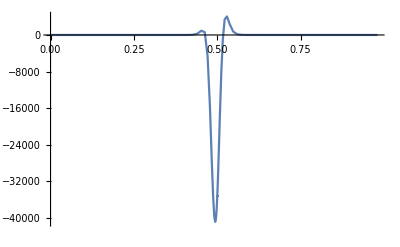

```mathematica
ListPlot[%80,Joined->True,PlotRange->All]
```

```mathematica
Block[{ω1,S,ω2,m=m1},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
Which[0<ω1<1&&ω2≥ω1,ℐ3[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m,M4,M3,M2,M1]+ℐ3[ω2/ω1,((1+1/ω2-ω1/ω2) ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m,M3,M4,M2,M1],ω2≥ω1&&ω1≥1,ℐ3[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m,M1,M2,M3,M4]+ℐ3[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][m,M2,M1,M3,M4],0<ω1<1&&ω1>ω2,ℐ3[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m,M1,M2,M4,M3]+ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][m,M2,M1,M4,M3],ω1≥1&&ω1>ω2,ℐ3[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m,M4,M3,M1,M2]+ℐ3[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m,M3,M4,M1,M2]]]
```

-14092.9

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][m1,M1,M2,M3,M4]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[1/ω1,(1-ω1+ω2)/ω1][ϕ4,ϕ3,ϕ2,ϕ1][m1,M4,M3,M2,M1]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][m1,M1,M2,M4,M3]]
```

3.83865

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ℳ0[ω2/ω1,(1-ω1+ω2)/ω1][ϕ3,ϕ4,ϕ2,ϕ1][m1,M3,M4,M2,M1]]
```

3.83865

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;Print[ω1=ω1S[S][M1,M2,M3,M4]];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ4,ϕ3,ϕ1,ϕ2][m1,M4,M3,M1,M2]]
```

0.981933

-3.35036×10^80+1.31763×10^67 ⅈ

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][m1,M3,M4,M1,M2]]
```

4.01135

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[1-ω1+ω2,ω2][ϕ2,ϕ1,ϕ3,ϕ4][M2,M1,M3,M4]]
```

0

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

-1.62385

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ1[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]]
```

4108.96

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ2[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ3,ϕ4,ϕ1,ϕ2][M3,M4,M1,M2]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.999409304759193060376486206219937002970254980027675628662109375,0.0000129484} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.26099×10^209 和 2.18188×10^209.

5.04402×10^209

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];If[ω1^2+ω2+ω2^2<ω1+2 ω1 ω2,-4 g^2 (NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,0,x/(ω2/(1-ω1+ω2))-λ}]+NIntegrate[(ω2 ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[y] ϕ1[x] ϕ2[(((y-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/((1-ω1+ω2) ((y ω2)/(1-ω1+ω2)-x)^2),{x,0,1},{y,x/(ω2/(1-ω1+ω2))+λ,1}]-(2 NIntegrate[(ϕ3[(x+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ4[x/(ω2/(1-ω1+ω2))] ϕ1[x] ϕ2[(((x/(ω2/(1-ω1+ω2))-1) ω2)/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ),0]]
```

0

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},MaxRecursion->50]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 2000 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 5.54003×10^6 和 4.90296×10^6.

5.54003×10^6

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];NIntegrate[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ3[ω1-ω2+x (1-ω1+ω2)] ϕ4[y] ϕ1[x] ϕ2[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,(x (1-ω1+ω2))/ω2-λ}]]
```

1.30171×10^183

```mathematica
Block[{ω1,S,ω2,ex},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
ex=(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1];NIntegrate[ex,{x,0,1},{y,(x (1-ω1+ω2))/ω2+λ,1},MaxRecursion->50,PrecisionGoal->15]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 2000 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.10072×10^213 和 2.99925×10^206.

-1.10072×10^213

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];(2 NIntegrate[(ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[(x (1-ω1+ω2))/ω2] ϕ3[x] ϕ4[(x+ω1-x ω1-ω2+x ω2)/ω1])/(ω2/(1-ω1+ω2)),{x,0,1}])/λ]
```

2.68909×10^200

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2),{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];Plot3D[(1-ω1+ω2)/((y+(x (-1+ω1-ω2))/ω2)^2 ω2) ϕ1[ω1-ω2+x (1-ω1+ω2)] ϕ2[y] ϕ3[x] ϕ4[1+((-1+y) ω2)/ω1],{x,0,1},{y,0,1},PlotRange->All]]
```

-Graphics3D-

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℐ3[(1-ω1+ω2)/ω2,1/ω2][ϕ2,ϕ1,ϕ4,ϕ3][M2,M1,M4,M3]]
```

2.13307×10^6

```mathematica
Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];ℳ1[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ4,ϕ3][M1,M2,M4,M3]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.000590695,0.99998705161026963496755440557323124650679346814285963773727416992} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.25434×10^209-9.59962×10^195 ⅈ 和 2.17036×10^209.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

-5.0174×10^209+4.18059×10^191 ⅈ

```mathematica
Clear[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
SetSharedVariable[M1,M2,M3,M4,ϕ1,ϕ2,ϕ3,ϕ4]
```

```mathematica
Table[{M1,ϕ1}={Mn[#][ValsB],ϕn[#][ΦB]}&[n1];
{M2,ϕ2}={Mn[#][ValsB],ϕn[#][ΦB]}&[n2];
{M3,ϕ3}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];
{M4,ϕ4}={Mn[#][ValsB],ϕn[#][ΦB]}&[0];Block[{ω1,S,ω2},S=(M1+M2+0.01)^2;ω1=ω1S[S][M1,M2,M3,M4];ω2=ω2S[S][M1,M2,M3,M4];
EXPR[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4][M1,M2,M3,M4]],{n1,0,5,1},{n2,0,5,1}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

$Aborted

```mathematica
ParallelTable[ℳ1[M1,M2,M3,M4][ω1/(ω2p[ω1][M1,M2,M3,M4]),1/(ω2p[ω1][M1,M2,M3,M4])][ϕ1,ϕ2,ϕ3,ϕ4],{ω1,0.1,0.9,0.1}]
```

{3.57115×10^-7,3.31586×10^-6,0.0000202997,0.000115472,0.000746742,0.00661315,0.118411,16.65,1778.83}

```mathematica
?EXPR
```

Global`EXPR

EXPR[ω1_,ω2_][Ma_,Mb_,Mc_,Md_][ϕ1_,ϕ2_,ϕ3_,ϕ4_]=ℳ0[ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/((1+1/ω2-ω1/ω2) ω2),ω1/((1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1+1/ω2-ω1/ω2) ω2,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1-ω1+ω2),ω1/(1-ω1+ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[(1-ω1+ω2)/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[ω2/(1+ω2-(1+1/ω2-ω1/ω2) ω2),((1+1/ω2-ω1/ω2) ω2)/(1+ω2-(1+1/ω2-ω1/ω2) ω2)][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ0[1/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2)),(1-ω1+ω2)/(ω2 (1+1/ω2-(1-ω1+ω2)/ω2))][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]+ℳ1[Ma,Mb,Mc,Md][ω1/ω2,1/ω2][ϕ1,ϕ2,ϕ3,ϕ4]

```mathematica
FindRoot[√(Sω1[ω1][M1,M2,M3,M4])==241.137,{ω1,0.9,0.99}]
```

{ω1→0.882942}

```mathematica
Reduce[1/(ω2p[ω1][M1,M2,M3,M4])>(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])&&(1-ω1+ω2p[ω1][M1,M2,M3,M4])/(ω2p[ω1][M1,M2,M3,M4])>1,ω1]
```

$Aborted

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[1/ω2>(1-ω1+ω2)/ω2&&(1-ω1+ω2)/ω2>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[ω2>ω1&&ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
Block[{ω1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; ω1/.FindInstance[(1-ω1+ω2)/ω1>1/ω1&&1/ω1>1&&0<ω1<1,ω1,100]]
```

ω1

```mathematica
ω1/.FindInstance[ω2p[ω1][M1,M2,M3,M4]>ω1&&ω1>1&&0<ω1<1,ω1,100]
```

ω1

```mathematica
Block[{ω1=0.1,ω2},ω2=ω2n[ω1][M1,M2,M3,M4]; Print[1/ω2>(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])&&(1-ω1+ω2n[ω1][M1,M2,M3,M4])/(ω2n[ω1][M1,M2,M3,M4])>1&&0<ω1<1];NIntegrate[(M3^2+M4^2/(ω1/(1-ω1+ω2))+M1^2/(x-ω2/(1-ω1+ω2))+M1^2/(x-1)-M1^2/(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))-M1^2/x) ϕ1[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(1+ω1/(1-ω1+ω2)-ω2/(1-ω1+ω2))] ϕ2[x/(ω2/(1-ω1+ω2))] ϕ3[x] ϕ4[(x-ω2/(1-ω1+ω2)+ω1/(1-ω1+ω2))/(ω1/(1-ω1+ω2))],{x,0,1}]]
```

False

8.83407707562666×10^916

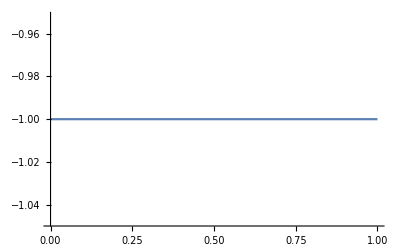

```mathematica
Plot[ω2n[ω1][M1,M2,M3,M4],{ω1,0,1}]
```

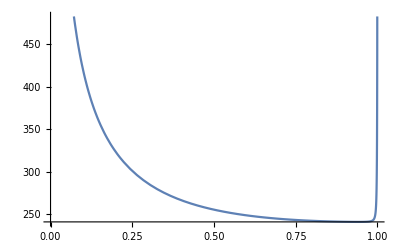

```mathematica
Plot[√(Sω1[ω1][M1,M2,M3,M4]),{ω1,0,1}]
```

```mathematica
Block[{ω1=0.8829424796893336,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]]
```

1955.93

```mathematica
Block[{ω1=0.907479105147823,ω2,Sen},ω2=ω2p[ω1][M1,M2,M3,M4];Sen=√(Sω1[ω1][M1,M2,M3,M4]);If[ω2∈Reals&&Sen∈Reals,Print["ω1=",ω1,"    ω2=",ω2];{Sen,ℳone[ω1,ω2][M1][ϕ1,ϕ2,ϕ3,ϕ4]},Print["Overflow: ω1=",ω1]]]
```

ω1=0.907479    ω2=0.708776

NIntegrate::ncvb: 在接近 {x,y} = {0.47396,0.589163} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

NIntegrate::ncvb: 在接近 {x,y} = {0.526042,0.410879} 处的 x 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 7087.77 和 143060..

{244.244,-113404.}

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];𝒞[ℳ0[ω1,ω2]][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

0.09278

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];ℳ1[M1][ω1,ω2][ϕ1,ϕ2,ϕ3,ϕ4]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

-3.46707×10^259

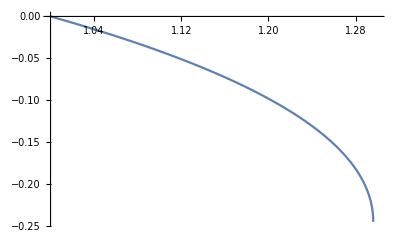

```mathematica
Plot[(ω2p[ω1][M1,M2,M3,M4])/ω1,{ω1,1,1.3}]
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.429446,0.907482} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -9.1960468217209363414030970359671991396517715069998422535022594849×10^1780+6.6644443576245410010334590115150447725581246899922275744416000763×10^1767 ⅈ 和 2.8418655168893182884967858465873180630766840277546920593796254944×10^1780.

-9.19604682172094×10^1780+6.7×10^1767 ⅈ

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,0,x/ω1-λ}]+NIntegrate[ω1/(y ω1-x)^2 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[y]ϕ3[x]ϕ4[((y-1) ω1+ω2)/ω2],{x,0,1},{y,x/ω1+λ,1}]-2/λ NIntegrate[1/ω1 ϕ1[(x+ω2-ω1)/(1+ω2-ω1)]ϕ2[x/ω1]ϕ3[x]ϕ4[((x/ω1-1) ω1+ω2)/ω2],{x,0,1}]]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x,y} = {0.99972774468308135838688632812676360117620788514614105224609375,9.83724×10^-6} 处的 y 中进行 18 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.33383×10^258 和 8.91081×10^258.

4.33383×10^258

```mathematica
NI1[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,0,(ω1-ω2+x ω2)/ω1-λ}]
NI2[ω1_,ω2_][x_?NumberQ]:=NIntegrate[(ω1 ω2)/((y-1) ω1+(1-x)ω2)^2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[y]ϕ3[y ω1]ϕ4[x],{y,(ω1-ω2+x ω2)/ω1+λ,1}]
```

```mathematica
λ=10^-4;
```

```mathematica
Block[{ω1=0.907479105147823,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[NI1[ω1,ω2][x],{x,0,1}]+NIntegrate[NI2[ω1,ω2][x],{x,0,1}]-2/λ NIntegrate[ω1 ω2 ϕ1[(x ω2)/(1+ω2-ω1)]ϕ2[(ω1-ω2+x ω2)/ω1]ϕ3[((ω1-ω2+x ω2)/ω1 )ω1]ϕ4[x],{x,0,1}])]
```

$Aborted

```mathematica
Table[Block[{ω1=0.3,ω2},ω2=ω2p[ω1][M1,M2,M3,M4];-4 g^2(NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,0,x-λ}]+NIntegrate[1/(y-x)^2 ϕ1[x ω2]ϕ2[y]ϕ3[y ω1]ϕ4[x],{x,λ,1-λ},{y,x+λ,1}]-2/λ NIntegrate[ ϕ1[x ω2]ϕ2[x]ϕ3[x ω1]ϕ4[x],{x,λ,1-λ}])],{λ,Table[10^-m,{m,2,7,1}]}]
```

{19.4562,19.7495,19.7852,19.7698,19.711,19.3019}

-7.96119×10^90+9.01471×10^71 ⅈ